```mathematica
(*idk if i will need these or not*)
(*These functions are to precompute the time integrals*)
(*Compute the partitions of the list x*)
partition[{x_}]:={{{x}}};
partition[{r__,x_}]:=Join@@(ReplaceList[#,{{b___,{S__},a___}:>{b,{S,x},a},{S__}:>{S,{x}}}]&/@partition[{r}]);
```

```mathematica
(*Kimura's eigenvalues*)
KimuraEig[i_]:=1/2*i*(i+1); 
(*The inside of all the time integrals*)
integrand[k_]:=Exp[Sum[( KimuraEig[m[i+1]] - KimuraEig[m[i]] - (2^(1+j[i])* Ne * VG / W))s[i],{i,1,k}]];
```

```mathematica
(*lets see what the inside of a 3 fold time integral would look like*)
k=3
integrand[k]
```

3

ⅇ^((-(2^(1+j[1]) Ne VG)/W-1/2 m[1] (1+m[1])+1/2 m[2] (1+m[2])) s[1]+(-(2^(1+j[2]) Ne VG)/W-1/2 m[2] (1+m[2])+1/2 m[3] (1+m[3])) s[2]+(-(2^(1+j[3]) Ne VG)/W-1/2 m[3] (1+m[3])+1/2 m[4] (1+m[4])) s[3])

```mathematica
integrand[k] /. {m[1 ]->m[2], VG ->1}
```

ⅇ^(-(2^(1+j[1]) Ne s[1])/W+(-(2^(1+j[2]) Ne)/W-1/2 m[2] (1+m[2])+1/2 m[3] (1+m[3])) s[2]+(-(2^(1+j[3]) Ne)/W-1/2 m[3] (1+m[3])+1/2 m[4] (1+m[4])) s[3])

```mathematica
sLimits[k_] := Join[{{s[k],0,t}},Reverse[Table[{s[j],0,s[j+1]},{j,1,k-1}]]];
sLimits[k]
```

{{s[3],0,t},{s[2],0,s[3]},{s[1],0,s[2]}}

```mathematica
Integrate[integrand[k],Evaluate[Sequence@@sLimits[k]]]
```

(8 W^3 (1/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne VG+W (m[1]+m[1]^2-m[4] (1+m[4]))))-1/((2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[2]+2^j[3]) Ne VG+W (m[2]+m[2]^2-m[4] (1+m[4]))))+(2^(2+j[1]) Ne VG+W (m[1]+m[1]^2-m[2] (1+m[2])))/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (2^(2+j[3]) Ne VG+W (m[3]+m[3]^2-m[4] (1+m[4]))))+ⅇ^(-(t (2^(2+j[3]) Ne VG+W (m[3]+m[3]^2-m[4] (1+m[4]))))/(2 W)) (-(ⅇ^(-1/2 t ((4 (2^j[1]+2^j[2]) Ne VG)/W+m[1]+m[1]^2-m[3] (1+m[3])))/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne VG+W (m[1]+m[1]^2-m[4] (1+m[4])))))+ⅇ^(-1/2 t ((2^(2+j[2]) Ne VG)/W+m[2]+m[2]^2-m[3] (1+m[3])))/((2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[2]+2^j[3]) Ne VG+W (m[2]+m[2]^2-m[4] (1+m[4]))))+(-2^(2+j[1]) Ne VG+W (-m[1]-m[1]^2+m[2]+m[2]^2))/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (2^(2+j[3]) Ne VG+W (m[3]+m[3]^2-m[4] (1+m[4])))))))/(2^(2+j[1]) Ne VG+W (m[1]+m[1]^2-m[2] (1+m[2])))

```mathematica
Integrate[integrand[k]/. {m[1 ]->m[2], VG ->1},Evaluate[Sequence@@sLimits[k]]]
```

1/Ne 2^(1-j[1]) W^3 ((ⅇ^(-1/2 t ((4 (2^j[2]+2^j[3]) Ne)/W+m[2]+m[2]^2-m[4] (1+m[4]))))/((2^(2+j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))))-(ⅇ^(-1/2 t ((4 (2^j[1]+2^j[2]+2^j[3]) Ne)/W+m[2]+m[2]^2-m[4] (1+m[4]))))/((4 (2^j[1]+2^j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))))-(2^(2+j[1]) ⅇ^(-1/2 t ((2^(2+j[3]) Ne)/W+m[3]+m[3]^2-m[4] (1+m[4]))) Ne)/((2^(2+j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (2^(2+j[3]) Ne+W (m[3]+m[3]^2-m[4] (1+m[4]))))+(2^(2+j[1]) Ne)/((4 (2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))) (2^(2+j[3]) Ne+W (m[3]+m[3]^2-m[4] (1+m[4])))))

```mathematica
Integrate[integrand[k],Evaluate[Sequence@@sLimits[k]]] /. {m[1 ]->m[2], VG ->1}
```

(4 W^2 (-2 W (1/((2^(2+j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))))-1/((4 (2^j[1]+2^j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))))-(2^(2+j[1]) Ne)/((2^(2+j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (2^(2+j[3]) Ne+W (m[3]+m[3]^2-m[4] (1+m[4])))))+2 ⅇ^(-(t (2^(2+j[3]) Ne+W (m[3]+m[3]^2-m[4] (1+m[4]))))/(2 W)) W ((ⅇ^(-1/2 t ((2^(2+j[2]) Ne)/W+m[2]+m[2]^2-m[3] (1+m[3]))))/((2^(2+j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))))-(ⅇ^(-1/2 t ((4 (2^j[1]+2^j[2]) Ne)/W+m[2]+m[2]^2-m[3] (1+m[3]))))/((4 (2^j[1]+2^j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne+W (m[2]+m[2]^2-m[4] (1+m[4]))))-(2^(2+j[1]) Ne)/((2^(2+j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]) Ne+W (m[2]+m[2]^2-m[3] (1+m[3]))) (2^(2+j[3]) Ne+W (m[3]+m[3]^2-m[4] (1+m[4])))))))/(2^(2+j[1]) Ne+W (m[2]+m[2]^2-m[2] (1+m[2])))

```mathematica
a = Integrate[integrand[k],Evaluate[Sequence@@sLimits[k]]] /. {m[1 ]->m[2], VG ->0} 
b = Integrate[integrand[k]/. {m[1 ]->m[2], VG ->0},Evaluate[Sequence@@sLimits[k]]]
```

0

1/((m[2]-m[3])^2 (1+m[2]+m[3])^2)((8 (-2 m[2]-2 m[2]^2+m[3]+m[3]^2+m[4]+m[4]^2))/((m[2]-m[4])^2 (1+m[2]+m[4])^2)+8/(m[3]+m[3]^2-m[4] (1+m[4]))+ⅇ^(-1/2 t (m[2]-m[4]) (1+m[2]+m[4])) ((4 t (m[2]+m[2]^2-m[3] (1+m[3])))/((m[2]-m[4]) (1+m[2]+m[4]))+(8 (2 m[2]+2 m[2]^2-m[3]-m[3]^2-m[4] (1+m[4])))/((m[2]-m[4])^2 (1+m[2]+m[4])^2)-(8 ⅇ^(1/2 t (m[2]-m[3]) (1+m[2]+m[3])))/(m[3]+m[3]^2-m[4] (1+m[4]))))

```mathematica
FullSimplify[a == b]
```

1/((m[2]-m[3])^2 (1+m[2]+m[3])^2)((8 (-2 m[2] (1+m[2])+m[3]+m[3]^2+m[4]+m[4]^2))/((m[2]-m[4])^2 (1+m[2]+m[4])^2)+8/(m[3]+m[3]^2-m[4] (1+m[4]))+ⅇ^(-1/2 t (m[2]-m[4]) (1+m[2]+m[4])) ((4 t (m[2]-m[3]) (1+m[2]+m[3]))/((m[2]-m[4]) (1+m[2]+m[4]))-(8 ⅇ^(1/2 t (m[2]-m[3]) (1+m[2]+m[3])))/(m[3]+m[3]^2-m[4] (1+m[4]))+(16 m[2] (1+m[2])-8 (m[3]+m[3]^2+m[4]+m[4]^2))/((m[2]-m[4])^2 (1+m[2]+m[4])^2)))==0

```mathematica
(*Define the limits of the k fold sum over the j_i s *)
jLimits[k_] := Table[{j[i],0,1},{i,1,k}];
jLimits[k]
```

{{j[1],0,1},{j[2],0,1},{j[3],0,1}}

```mathematica
(*Define the limits of the k+1 fold infinite sums. Truncating after n_ terms*)
mLimits[k_, n_ ] := Join[{{m[1],1,n}},Table[{m[j],m[j-1]-2,m[j-1]+2,1},{j,2,k+1}]];
n = 10;
```

```mathematica
mLimits[k,n]
```

{{m[1],1,10},{m[2],-2+m[1],2+m[1],1},{m[3],-2+m[2],2+m[2],1},{m[4],-2+m[3],2+m[3],1}}

```mathematica
(*We can precompute the integrral over time for a given k.*)
computeTimeInts[k_] :=  Integrate[integrand[k],Evaluate[Sequence@@sLimits[k]]];
```

```mathematica
computeTimeInts[k]
```

(4 W^2 (-2 W (-(1/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne VG+W (m[1]+m[1]^2-m[4] (1+m[4])))))+1/((2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[2]+2^j[3]) Ne VG+W (m[2]+m[2]^2-m[4] (1+m[4]))))+(-2^(2+j[1]) Ne VG+W (-m[1]-m[1]^2+m[2]+m[2]^2))/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (2^(2+j[3]) Ne VG+W (m[3]+m[3]^2-m[4] (1+m[4])))))+2 ⅇ^(-(t (2^(2+j[3]) Ne VG+W (m[3]+m[3]^2-m[4] (1+m[4]))))/(2 W)) W (-(ⅇ^(-1/2 t ((4 (2^j[1]+2^j[2]) Ne VG)/W+m[1]+m[1]^2-m[3] (1+m[3])))/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (4 (2^j[1]+2^j[2]+2^j[3]) Ne VG+W (m[1]+m[1]^2-m[4] (1+m[4])))))+ⅇ^(-1/2 t ((2^(2+j[2]) Ne VG)/W+m[2]+m[2]^2-m[3] (1+m[3])))/((2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (4 (2^j[2]+2^j[3]) Ne VG+W (m[2]+m[2]^2-m[4] (1+m[4]))))+(-2^(2+j[1]) Ne VG+W (-m[1]-m[1]^2+m[2]+m[2]^2))/((4 (2^j[1]+2^j[2]) Ne VG+W (m[1]+m[1]^2-m[3] (1+m[3]))) (2^(2+j[2]) Ne VG+W (m[2]+m[2]^2-m[3] (1+m[3]))) (2^(2+j[3]) Ne VG+W (m[3]+m[3]^2-m[4] (1+m[4])))))))/(2^(2+j[1]) Ne VG+W (m[1]+m[1]^2-m[2] (1+m[2])))

```mathematica
integrandPart[myPartition_,k_]:=Module[{curFun,firstElement,block,curElement},
curFun = integrand[k];
 For[a=1,a≤Length[myPartition],a++,
firstElement = myPartition[[a,1]];
For[b=2,b≤Length[myPartition[[a]]],b++,
curElement = myPartition[[a,b]];
curFun = curFun/.m[curElement]->m[firstElement];
];
];
curFun//FullSimplify
]
```

```mathematica
(*TODO think of better names for these functions*)
computeInts[k_]:=Module[{curParts,curLimits,curIntegrand,curInts,j},
curParts = partition[Table[j,{j,1,k+1}]];
curLimits = sLimits[k];
For[j=1,j≤Length[curParts],j++,
curIntegrand=integrandPart[curParts[[j]],k];
curInts[curParts[[j]]]=Integrate[curIntegrand,Evaluate[Sequence@@curLimits]];
];
Return[curInts]
]
```

```mathematica
(*Functions to compute the path integral to order k*)
(*Find the partition given the current state of the summation*)
findEquiv[vals_] := Module[{tempPart},
tempPart=Function[val,Flatten[Position[vals,val]]]/@Union[vals];
Sort[tempPart,Less[First[#1],First[#2]]&]
]
```

```mathematica
(*These functions are to compute the space integrals involving the Gegenbauer functions*)
(*The normalizations for the Gegenbauer polynomials*)
gegenbauerNorm[n_,λ_:3/2] := π*2^(1-2*λ)*Gamma[n+2*λ]/(Factorial[n]*(n+λ)*Gamma[λ]^2);
```

```mathematica
f[0,0]=1;
f[a_,b_]:=a^b
```

```mathematica
(*TODO quadruple check this expression*)
(*Maybe replace the f function with an if statement*)
computeSpaceInt[a_,b_,j_] := 1/(2^(4+j))( KroneckerDelta[a,b]* gegenbauerNorm[a] - 
(f[(1/(3+2a) * 
((a+1)*KroneckerDelta[a,b-1]*gegenbauerNorm[a+1]+
(a+2)*KroneckerDelta[a,b+1]*gegenbauerNorm[a-1])),(1-j) ] * (*3rdd to last partenthesis on this line was missing. check if this fixed*)
f[(1/((2*a+3)*(2*b+3))*
((a+1)*(b+1)*KroneckerDelta[a,b]*gegenbauerNorm[a+1]+
(a+1)*(b+2)*KroneckerDelta[a,b-2]*gegenbauerNorm[a+1]+
(a+2)*(b+1)*KroneckerDelta[a,b+2]*gegenbauerNorm[a-1]+
(a+2)*(b+2)*KroneckerDelta[a,b]*gegenbauerNorm[a-1])),j]))
```

```mathematica
computeSpaceInt[3,2,0]
gegenbauerNorm[2]
```

-5/42

24/7

```mathematica
(*Define the coefficients from Kimura's solution*)
kimuraCoefficient[i_]:= If[i>0,(2*i+1)/(i*(i+1)),0];
```

```mathematica
(*Kimura's neutral transition density*)
(*I pulled the 4x(1-x) into the leading coefficient*)
Kimura[x_,y_,t_,n_]:= Module[{i},Sum[4*(2*i+1)*x*(1-x)/(i*(i+1))*GegenbauerC[i-1,3/2,1-2*x]*GegenbauerC[i-1,3/2,1-2*y]*Exp[-1/2*i*(i+1)*t],{i,1,n}]
]
```

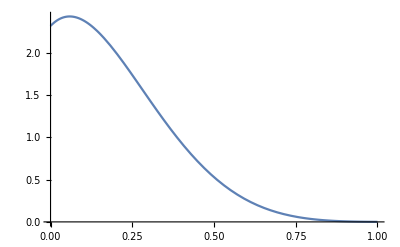

```mathematica
Plot[Kimura[x,y,t,50]/.{x->.2,t->.2},{y,0,1}]
```

```mathematica
Integrate[Kimura[x,y,t,10],{y,0,1}]/. {x->.2,t->.5}
```

0.604253

```mathematica
For[n = 1, n ≤ 20, n ++,
Print[Kimura[x,y,t,n]/.{x->.2,t->.2, y->.4}]
]
```

0.785982

1.1021

0.940175

0.978341

0.952694

0.938279

0.938303

0.937648

0.937601

0.937609

0.937608

0.937608

0.937608

«7 more identical outputs»

```mathematica
(**)
kthterm[x_,y_,t_,k_,n_, Ne_, α_, Λ_, W_,VG_] := Module[{kfoldtimeint, mlims, jlims},
mlims = mLimits[k,n];
jlims = jLimits[k];
kfoldtimeint=  computeInts[k];
4 x(1-x)(8 Ne^2 α Λ / W^2)^k* Sum[If[Negative@Min@Table[m[i],{i,1,k+1}], 0, 
GegenbauerC[m[1]-1,3/2,1-2*x]*GegenbauerC[m[k+1]-1,3/2,1-2*y] *Exp[-KimuraEig[m[k+1]]*t]* Product[kimuraCoefficient[m[i]],{i,1,k+1}] * 
Sum[
Product[(2 VG)^(1-j[i])(-α*Λ)^j[i] computeSpaceInt[m[i]-1, m[i+1]-1, j[i]],{i, 1, k}] *
kfoldtimeint[findEquiv[Table[m[i],{i,1,k+1}]]], Evaluate[Sequence@@jlims]]
], Evaluate[Sequence@@mlims]]
]
```

```mathematica
For[i = 1, i ≤10, i++,
Print[GegenbauerC[i-1,3/2,1-2*y]/. {y->0.2}]
]
```

1

1.8

1.2

-0.72

-2.472

-2.39904

-0.234752

2.43994

3.37501

1.56398

```mathematica
k = 2
n = 10
```

2

10

```mathematica
oldversion = kthterm[x,y,t,k,n,Ne,α,Λ, W, VG]
```

1/W^4 256 Ne^4 (1-x) x α^2 Λ^2 ((3 ⅇ^-t VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (4+(4 Ne VG)/W))) W)/(4 Ne VG+4 W)))/(160 (4 Ne VG-4 W))+(ⅇ^-t VG^2 W^2 ((1-ⅇ^(-1/2 t (4+(4 Ne VG)/W)))/(4 Ne VG+4 W)-(1-ⅇ^(-1/2 t (10+(8 Ne VG)/W)))/(8 Ne VG+10 W)) (-3/2+15/2 (1-2 x)^2))/(20 (4 Ne VG+6 W))+(ⅇ^(-6 t) VG^2 (-(1-ⅇ^(-1/2 t (-10+(8 Ne VG)/W)))/(8 Ne VG-10 W)+(1-ⅇ^(-1/2 t (-6+(4 Ne VG)/W)))/(4 Ne VG-6 W)) W^2 (-3/2+15/2 (1-2 y)^2))/(20 (4 Ne VG-4 W))+(ⅇ^(-6 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (-6+(4 Ne VG)/W))) W)/(4 Ne VG-6 W)) (-3/2+15/2 (1-2 x)^2) (-3/2+15/2 (1-2 y)^2))/(120 (4 Ne VG+6 W))+(5 ⅇ^(-6 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (8+(4 Ne VG)/W))) W)/(4 Ne VG+8 W)) (-3/2+15/2 (1-2 x)^2) (-3/2+15/2 (1-2 y)^2))/(576 (4 Ne VG-8 W))+(ⅇ^(-6 t) VG^2 W^2 ((1-ⅇ^(-1/2 t (8+(4 Ne VG)/W)))/(4 Ne VG+8 W)-(1-ⅇ^(-1/2 t (18+(8 Ne VG)/W)))/(8 Ne VG+18 W)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-3/2+15/2 (1-2 y)^2))/(36 (4 Ne VG+10 W))+(3 ⅇ^(-10 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (-8+(4 Ne VG)/W))) W)/(4 Ne VG-8 W)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-15/2 (1-2 y)+35/2 (1-2 y)^3))/(448 (4 Ne VG+8 W))+(3 ⅇ^(-10 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (10+(4 Ne VG)/W))) W)/(4 Ne VG+10 W)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-15/2 (1-2 y)+35/2 (1-2 y)^3))/(440 (4 Ne VG-10 W))+(ⅇ^(-10 t) VG^2 W^2 ((1-ⅇ^(-1/2 t (10+(4 Ne VG)/W)))/(4 Ne VG+10 W)-(1-ⅇ^(-1/2 t (22+(8 Ne VG)/W)))/(8 Ne VG+22 W)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-15/2 (1-2 y)+35/2 (1-2 y)^3))/(44 (4 Ne VG+12 W))+(3 ⅇ^(-10 t) VG^2 (-(1-ⅇ^(-1/2 t (-14+(8 Ne VG)/W)))/(8 Ne VG-14 W)+(1-ⅇ^(-1/2 t (-8+(4 Ne VG)/W)))/(4 Ne VG-8 W)) W^2 (1-2 x) (-15/2 (1-2 y)+35/2 (1-2 y)^3))/(28 (4 Ne VG-6 W))+(ⅇ^(-15 t) VG^2 (-(1-ⅇ^(-1/2 t (-18+(8 Ne VG)/W)))/(8 Ne VG-18 W)+(1-ⅇ^(-1/2 t (-10+(4 Ne VG)/W)))/(4 Ne VG-10 W)) W^2 (-3/2+15/2 (1-2 x)^2) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4))/(36 (4 Ne VG-8 W))+(ⅇ^(-15 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (-10+(4 Ne VG)/W))) W)/(4 Ne VG-10 W)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4))/(180 (4 Ne VG+10 W))+(7 ⅇ^(-15 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (12+(4 Ne VG)/W))) W)/(4 Ne VG+12 W)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4))/(1248 (4 Ne VG-12 W))+(ⅇ^(-15 t) VG^2 W^2 ((1-ⅇ^(-1/2 t (12+(4 Ne VG)/W)))/(4 Ne VG+12 W)-(1-ⅇ^(-1/2 t (26+(8 Ne VG)/W)))/(8 Ne VG+26 W)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4))/(52 (4 Ne VG+14 W))+(ⅇ^(-21 t) VG^2 (-(1-ⅇ^(-1/2 t (-22+(8 Ne VG)/W)))/(8 Ne VG-22 W)+(1-ⅇ^(-1/2 t (-12+(4 Ne VG)/W)))/(4 Ne VG-12 W)) W^2 (-15/2 (1-2 x)+35/2 (1-2 x)^3) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5))/(44 (4 Ne VG-10 W))+(5 ⅇ^(-21 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (-12+(4 Ne VG)/W))) W)/(4 Ne VG-12 W)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5))/(1056 (4 Ne VG+12 W))+(ⅇ^(-21 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (14+(4 Ne VG)/W))) W)/(4 Ne VG+14 W)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5))/(210 (4 Ne VG-14 W))+1/(60 (4 Ne VG+16 W))ⅇ^(-21 t) VG^2 W^2 ((1-ⅇ^(-1/2 t (14+(4 Ne VG)/W)))/(4 Ne VG+14 W)-(1-ⅇ^(-1/2 t (30+(8 Ne VG)/W)))/(8 Ne VG+30 W)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5)+(ⅇ^(-28 t) VG^2 (-(1-ⅇ^(-1/2 t (-26+(8 Ne VG)/W)))/(8 Ne VG-26 W)+(1-ⅇ^(-1/2 t (-14+(4 Ne VG)/W)))/(4 Ne VG-14 W)) W^2 (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6))/(52 (4 Ne VG-12 W))+1/(728 (4 Ne VG+14 W))3 ⅇ^(-28 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (-14+(4 Ne VG)/W))) W)/(4 Ne VG-14 W)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6)+1/(2176 (4 Ne VG-16 W))9 ⅇ^(-28 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (16+(4 Ne VG)/W))) W)/(4 Ne VG+16 W)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6)+1/(68 (4 Ne VG+18 W))ⅇ^(-28 t) VG^2 W^2 ((1-ⅇ^(-1/2 t (16+(4 Ne VG)/W)))/(4 Ne VG+16 W)-(1-ⅇ^(-1/2 t (34+(8 Ne VG)/W)))/(8 Ne VG+34 W)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6)+1/(60 (4 Ne VG-14 W))ⅇ^(-36 t) VG^2 (-(1-ⅇ^(-1/2 t (-30+(8 Ne VG)/W)))/(8 Ne VG-30 W)+(1-ⅇ^(-1/2 t (-16+(4 Ne VG)/W)))/(4 Ne VG-16 W)) W^2 (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7)+1/(1920 (4 Ne VG+16 W))7 ⅇ^(-36 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (-16+(4 Ne VG)/W))) W)/(4 Ne VG-16 W)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7)+1/(1368 (4 Ne VG-18 W))5 ⅇ^(-36 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (18+(4 Ne VG)/W))) W)/(4 Ne VG+18 W)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7)+1/(76 (4 Ne VG+20 W))ⅇ^(-36 t) VG^2 W^2 ((1-ⅇ^(-1/2 t (18+(4 Ne VG)/W)))/(4 Ne VG+18 W)-(1-ⅇ^(-1/2 t (38+(8 Ne VG)/W)))/(8 Ne VG+38 W)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7)+1/(68 (4 Ne VG-16 W))ⅇ^(-45 t) VG^2 (-(1-ⅇ^(-1/2 t (-34+(8 Ne VG)/W)))/(8 Ne VG-34 W)+(1-ⅇ^(-1/2 t (-18+(4 Ne VG)/W)))/(4 Ne VG-18 W)) W^2 (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8)+1/(306 (4 Ne VG+18 W))ⅇ^(-45 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (-18+(4 Ne VG)/W))) W)/(4 Ne VG-18 W)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8)+1/(3360 (4 Ne VG-20 W))11 ⅇ^(-45 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (20+(4 Ne VG)/W))) W)/(4 Ne VG+20 W)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8)+1/(76 (4 Ne VG-18 W))ⅇ^(-55 t) VG^2 (-(1-ⅇ^(-1/2 t (-38+(8 Ne VG)/W)))/(8 Ne VG-38 W)+(1-ⅇ^(-1/2 t (-20+(4 Ne VG)/W)))/(4 Ne VG-20 W)) W^2 (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9)+1/(3040 (4 Ne VG+20 W))9 ⅇ^(-55 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (-20+(4 Ne VG)/W))) W)/(4 Ne VG-20 W)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9)+1/(1012 (4 Ne VG-22 W))3 ⅇ^(-55 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (22+(4 Ne VG)/W))) W)/(4 Ne VG+22 W)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9)+1/(84 (4 Ne VG-20 W))ⅇ^(-66 t) VG^2 (-(1-ⅇ^(-1/2 t (-42+(8 Ne VG)/W)))/(8 Ne VG-42 W)+(1-ⅇ^(-1/2 t (-22+(4 Ne VG)/W)))/(4 Ne VG-22 W)) W^2 (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-693/256+45045/256 (1-2 y)^2-225225/128 (1-2 y)^4+765765/128 (1-2 y)^6-2078505/256 (1-2 y)^8+969969/256 (1-2 y)^10)+1/(92 (4 Ne VG-22 W))ⅇ^(-78 t) VG^2 (-(1-ⅇ^(-1/2 t (-46+(8 Ne VG)/W)))/(8 Ne VG-46 W)+(1-ⅇ^(-1/2 t (-24+(4 Ne VG)/W)))/(4 Ne VG-24 W)) W^2 (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-9009/256 (1-2 y)+225225/256 (1-2 y)^3-765765/128 (1-2 y)^5+2078505/128 (1-2 y)^7-4849845/256 (1-2 y)^9+2028117/256 (1-2 y)^11)+(3 ⅇ^(-3 t) VG^2 W^2 ((1-ⅇ^(-1/2 t (6+(4 Ne VG)/W)))/(4 Ne VG+6 W)-(1-ⅇ^(-1/2 t (14+(8 Ne VG)/W)))/(8 Ne VG+14 W)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (1-2 y))/(28 (4 Ne VG+8 W))+(3 ⅇ^(-3 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (-4+(4 Ne VG)/W))) W)/(4 Ne VG-4 W)) (1-2 x) (1-2 y))/(32 (4 Ne VG+4 W))+(3 ⅇ^(-3 t) VG^2 W (((-1+ⅇ^(-(4 Ne t VG)/W)) W)/(2 Ne VG)+(4 (1-ⅇ^(-1/2 t (6+(4 Ne VG)/W))) W)/(4 Ne VG+6 W)) (1-2 x) (1-2 y))/(28 (4 Ne VG-6 W))-(3 ⅇ^-t VG W^2 ((1-ⅇ^(-1/2 t (4+(4 Ne VG)/W)))/(4 Ne VG+4 W)-(1-ⅇ^(-1/2 t (18+(12 Ne VG)/W)))/(12 Ne VG+18 W)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) α Λ)/(560 (8 Ne VG+14 W))-(3 ⅇ^-t VG W^2 ((1-ⅇ^(-1/2 t (10+(8 Ne VG)/W)))/(8 Ne VG+10 W)-(1-ⅇ^(-1/2 t (18+(12 Ne VG)/W)))/(12 Ne VG+18 W)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) α Λ)/(560 (4 Ne VG+8 W))-(3 ⅇ^-t VG W^2 (-(1-ⅇ^(-1/2 t (4+(12 Ne VG)/W)))/(12 Ne VG+4 W)+(1-ⅇ^(-1/2 t (10+(8 Ne VG)/W)))/(8 Ne VG+10 W)) (1-2 x) α Λ)/(140 (4 Ne VG-6 W))-(ⅇ^(-6 t) VG W^2 ((1-ⅇ^(-1/2 t (-6+(4 Ne VG)/W)))/(4 Ne VG-6 W)-(1-ⅇ^(-1/2 t (8+(12 Ne VG)/W)))/(12 Ne VG+8 W)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-3/2+15/2 (1-2 y)^2) α Λ)/(280 (8 Ne VG+14 W))-(ⅇ^(-6 t) VG W^2 (-(1-ⅇ^(-1/2 t (8+(12 Ne VG)/W)))/(12 Ne VG+8 W)+(1-ⅇ^(-1/2 t (18+(8 Ne VG)/W)))/(8 Ne VG+18 W)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-3/2+15/2 (1-2 y)^2) α Λ)/(264 (4 Ne VG-10 W))-(5 ⅇ^(-6 t) VG W^2 ((1-ⅇ^(-1/2 t (8+(4 Ne VG)/W)))/(4 Ne VG+8 W)-(1-ⅇ^(-1/2 t (30+(12 Ne VG)/W)))/(12 Ne VG+30 W)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-3/2+15/2 (1-2 y)^2) α Λ)/(1584 (8 Ne VG+22 W))-(5 ⅇ^(-6 t) VG W^2 ((1-ⅇ^(-1/2 t (18+(8 Ne VG)/W)))/(8 Ne VG+18 W)-(1-ⅇ^(-1/2 t (30+(12 Ne VG)/W)))/(12 Ne VG+30 W)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-3/2+15/2 (1-2 y)^2) α Λ)/(1584 (4 Ne VG+12 W))-(ⅇ^(-6 t) VG ((1-ⅇ^(-1/2 t (-10+(8 Ne VG)/W)))/(8 Ne VG-10 W)-(1-ⅇ^(-1/2 t (-6+(12 Ne VG)/W)))/(12 Ne VG-6 W)) W^2 (1-2 x) (-3/2+15/2 (1-2 y)^2) α Λ)/(80 (4 Ne VG+4 W))-(5 ⅇ^(-6 t) VG W^2 (-(1-ⅇ^(-1/2 t (-6+(12 Ne VG)/W)))/(12 Ne VG-6 W)+(1-ⅇ^(-1/2 t (8+(4 Ne VG)/W)))/(4 Ne VG+8 W)) (1-2 x) (-3/2+15/2 (1-2 y)^2) α Λ)/(336 (8 Ne VG-14 W))-(3 ⅇ^(-10 t) VG (-(1-ⅇ^(-1/2 t (-18+(12 Ne VG)/W)))/(12 Ne VG-18 W)+(1-ⅇ^(-1/2 t (-8+(4 Ne VG)/W)))/(4 Ne VG-8 W)) W^2 (-15/2 (1-2 y)+35/2 (1-2 y)^3) α Λ)/(560 (8 Ne VG-10 W))-(3 ⅇ^(-10 t) VG (-(1-ⅇ^(-1/2 t (-18+(12 Ne VG)/W)))/(12 Ne VG-18 W)+(1-ⅇ^(-1/2 t (-14+(8 Ne VG)/W)))/(8 Ne VG-14 W)) W^2 (-15/2 (1-2 y)+35/2 (1-2 y)^3) α Λ)/(560 (4 Ne VG-4 W))-(ⅇ^(-10 t) VG ((1-ⅇ^(-1/2 t (-14+(8 Ne VG)/W)))/(8 Ne VG-14 W)-(1-ⅇ^(-1/2 t (-8+(12 Ne VG)/W)))/(12 Ne VG-8 W)) W^2 (-3/2+15/2 (1-2 x)^2) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α Λ)/(280 (4 Ne VG+6 W))-(ⅇ^(-10 t) VG W^2 (-(1-ⅇ^(-1/2 t (-8+(12 Ne VG)/W)))/(12 Ne VG-8 W)+(1-ⅇ^(-1/2 t (10+(4 Ne VG)/W)))/(4 Ne VG+10 W)) (-3/2+15/2 (1-2 x)^2) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α Λ)/(264 (8 Ne VG-18 W))-(ⅇ^(-10 t) VG W^2 ((1-ⅇ^(-1/2 t (-8+(4 Ne VG)/W)))/(4 Ne VG-8 W)-(1-ⅇ^(-1/2 t (10+(12 Ne VG)/W)))/(12 Ne VG+10 W)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α Λ)/(336 (8 Ne VG+18 W))-(7 ⅇ^(-10 t) VG W^2 (-(1-ⅇ^(-1/2 t (10+(12 Ne VG)/W)))/(12 Ne VG+10 W)+(1-ⅇ^(-1/2 t (22+(8 Ne VG)/W)))/(8 Ne VG+22 W)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α Λ)/(2288 (4 Ne VG-12 W))-(3 ⅇ^(-10 t) VG W^2 ((1-ⅇ^(-1/2 t (10+(4 Ne VG)/W)))/(4 Ne VG+10 W)-(1-ⅇ^(-1/2 t (36+(12 Ne VG)/W)))/(12 Ne VG+36 W)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α Λ)/(1144 (8 Ne VG+26 W))-(3 ⅇ^(-10 t) VG W^2 ((1-ⅇ^(-1/2 t (22+(8 Ne VG)/W)))/(8 Ne VG+22 W)-(1-ⅇ^(-1/2 t (36+(12 Ne VG)/W)))/(12 Ne VG+36 W)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α Λ)/(1144 (4 Ne VG+14 W))-(ⅇ^(-15 t) VG ((1-ⅇ^(-1/2 t (-18+(8 Ne VG)/W)))/(8 Ne VG-18 W)-(1-ⅇ^(-1/2 t (-10+(12 Ne VG)/W)))/(12 Ne VG-10 W)) W^2 (-15/2 (1-2 x)+35/2 (1-2 x)^3) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α Λ)/(336 (4 Ne VG+8 W))-(7 ⅇ^(-15 t) VG W^2 (-(1-ⅇ^(-1/2 t (-10+(12 Ne VG)/W)))/(12 Ne VG-10 W)+(1-ⅇ^(-1/2 t (12+(4 Ne VG)/W)))/(4 Ne VG+12 W)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α Λ)/(2288 (8 Ne VG-22 W))-(ⅇ^(-15 t) VG W^2 ((1-ⅇ^(-1/2 t (-10+(4 Ne VG)/W)))/(4 Ne VG-10 W)-(1-ⅇ^(-1/2 t (12+(12 Ne VG)/W)))/(12 Ne VG+12 W)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α Λ)/(396 (8 Ne VG+22 W))-(ⅇ^(-15 t) VG W^2 (-(1-ⅇ^(-1/2 t (12+(12 Ne VG)/W)))/(12 Ne VG+12 W)+(1-ⅇ^(-1/2 t (26+(8 Ne VG)/W)))/(8 Ne VG+26 W)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α Λ)/(390 (4 Ne VG-14 W))-1/(3120 (8 Ne VG+30 W))7 ⅇ^(-15 t) VG W^2 ((1-ⅇ^(-1/2 t (12+(4 Ne VG)/W)))/(4 Ne VG+12 W)-(1-ⅇ^(-1/2 t (42+(12 Ne VG)/W)))/(12 Ne VG+42 W)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α Λ-1/(3120 (4 Ne VG+16 W))7 ⅇ^(-15 t) VG W^2 ((1-ⅇ^(-1/2 t (26+(8 Ne VG)/W)))/(8 Ne VG+26 W)-(1-ⅇ^(-1/2 t (42+(12 Ne VG)/W)))/(12 Ne VG+42 W)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α Λ-(ⅇ^(-15 t) VG (-(1-ⅇ^(-1/2 t (-24+(12 Ne VG)/W)))/(12 Ne VG-24 W)+(1-ⅇ^(-1/2 t (-10+(4 Ne VG)/W)))/(4 Ne VG-10 W)) W^2 (1-2 x) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α Λ)/(84 (8 Ne VG-14 W))-(ⅇ^(-15 t) VG (-(1-ⅇ^(-1/2 t (-24+(12 Ne VG)/W)))/(12 Ne VG-24 W)+(1-ⅇ^(-1/2 t (-18+(8 Ne VG)/W)))/(8 Ne VG-18 W)) W^2 (1-2 x) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α Λ)/(84 (4 Ne VG-6 W))-(5 ⅇ^(-21 t) VG (-(1-ⅇ^(-1/2 t (-30+(12 Ne VG)/W)))/(12 Ne VG-30 W)+(1-ⅇ^(-1/2 t (-12+(4 Ne VG)/W)))/(4 Ne VG-12 W)) W^2 (-3/2+15/2 (1-2 x)^2) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α Λ)/(1584 (8 Ne VG-18 W))-(5 ⅇ^(-21 t) VG (-(1-ⅇ^(-1/2 t (-30+(12 Ne VG)/W)))/(12 Ne VG-30 W)+(1-ⅇ^(-1/2 t (-22+(8 Ne VG)/W)))/(8 Ne VG-22 W)) W^2 (-3/2+15/2 (1-2 x)^2) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α Λ)/(1584 (4 Ne VG-8 W))-(ⅇ^(-21 t) VG ((1-ⅇ^(-1/2 t (-22+(8 Ne VG)/W)))/(8 Ne VG-22 W)-(1-ⅇ^(-1/2 t (-12+(12 Ne VG)/W)))/(12 Ne VG-12 W)) W^2 (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α Λ)/(396 (4 Ne VG+10 W))-(ⅇ^(-21 t) VG W^2 (-(1-ⅇ^(-1/2 t (-12+(12 Ne VG)/W)))/(12 Ne VG-12 W)+(1-ⅇ^(-1/2 t (14+(4 Ne VG)/W)))/(4 Ne VG+14 W)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α Λ)/(390 (8 Ne VG-26 W))-1/(2288 (8 Ne VG+26 W))5 ⅇ^(-21 t) VG W^2 ((1-ⅇ^(-1/2 t (-12+(4 Ne VG)/W)))/(4 Ne VG-12 W)-(1-ⅇ^(-1/2 t (14+(12 Ne VG)/W)))/(12 Ne VG+14 W)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α Λ-1/(1360 (4 Ne VG-16 W))3 ⅇ^(-21 t) VG W^2 (-(1-ⅇ^(-1/2 t (14+(12 Ne VG)/W)))/(12 Ne VG+14 W)+(1-ⅇ^(-1/2 t (30+(8 Ne VG)/W)))/(8 Ne VG+30 W)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α Λ-1/(510 (8 Ne VG+34 W))ⅇ^(-21 t) VG W^2 ((1-ⅇ^(-1/2 t (14+(4 Ne VG)/W)))/(4 Ne VG+14 W)-(1-ⅇ^(-1/2 t (48+(12 Ne VG)/W)))/(12 Ne VG+48 W)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α Λ-1/(510 (4 Ne VG+18 W))ⅇ^(-21 t) VG W^2 ((1-ⅇ^(-1/2 t (30+(8 Ne VG)/W)))/(8 Ne VG+30 W)-(1-ⅇ^(-1/2 t (48+(12 Ne VG)/W)))/(12 Ne VG+48 W)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α Λ-(3 ⅇ^(-28 t) VG (-(1-ⅇ^(-1/2 t (-36+(12 Ne VG)/W)))/(12 Ne VG-36 W)+(1-ⅇ^(-1/2 t (-14+(4 Ne VG)/W)))/(4 Ne VG-14 W)) W^2 (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α Λ)/(1144 (8 Ne VG-22 W))-(3 ⅇ^(-28 t) VG (-(1-ⅇ^(-1/2 t (-36+(12 Ne VG)/W)))/(12 Ne VG-36 W)+(1-ⅇ^(-1/2 t (-26+(8 Ne VG)/W)))/(8 Ne VG-26 W)) W^2 (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α Λ)/(1144 (4 Ne VG-10 W))-1/(2288 (4 Ne VG+12 W))5 ⅇ^(-28 t) VG ((1-ⅇ^(-1/2 t (-26+(8 Ne VG)/W)))/(8 Ne VG-26 W)-(1-ⅇ^(-1/2 t (-14+(12 Ne VG)/W)))/(12 Ne VG-14 W)) W^2 (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α Λ-1/(1360 (8 Ne VG-30 W))3 ⅇ^(-28 t) VG W^2 (-(1-ⅇ^(-1/2 t (-14+(12 Ne VG)/W)))/(12 Ne VG-14 W)+(1-ⅇ^(-1/2 t (16+(4 Ne VG)/W)))/(4 Ne VG+16 W)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α Λ-1/(520 (8 Ne VG+30 W))ⅇ^(-28 t) VG W^2 ((1-ⅇ^(-1/2 t (-14+(4 Ne VG)/W)))/(4 Ne VG-14 W)-(1-ⅇ^(-1/2 t (16+(12 Ne VG)/W)))/(12 Ne VG+16 W)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α Λ-1/(2584 (4 Ne VG-18 W))5 ⅇ^(-28 t) VG W^2 (-(1-ⅇ^(-1/2 t (16+(12 Ne VG)/W)))/(12 Ne VG+16 W)+(1-ⅇ^(-1/2 t (34+(8 Ne VG)/W)))/(8 Ne VG+34 W)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α Λ-1/(5168 (8 Ne VG+38 W))9 ⅇ^(-28 t) VG W^2 ((1-ⅇ^(-1/2 t (16+(4 Ne VG)/W)))/(4 Ne VG+16 W)-(1-ⅇ^(-1/2 t (54+(12 Ne VG)/W)))/(12 Ne VG+54 W)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α Λ-1/(5168 (4 Ne VG+20 W))9 ⅇ^(-28 t) VG W^2 ((1-ⅇ^(-1/2 t (34+(8 Ne VG)/W)))/(8 Ne VG+34 W)-(1-ⅇ^(-1/2 t (54+(12 Ne VG)/W)))/(12 Ne VG+54 W)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α Λ-1/(3120 (8 Ne VG-26 W))7 ⅇ^(-36 t) VG (-(1-ⅇ^(-1/2 t (-42+(12 Ne VG)/W)))/(12 Ne VG-42 W)+(1-ⅇ^(-1/2 t (-16+(4 Ne VG)/W)))/(4 Ne VG-16 W)) W^2 (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α Λ-1/(3120 (4 Ne VG-12 W))7 ⅇ^(-36 t) VG (-(1-ⅇ^(-1/2 t (-42+(12 Ne VG)/W)))/(12 Ne VG-42 W)+(1-ⅇ^(-1/2 t (-30+(8 Ne VG)/W)))/(8 Ne VG-30 W)) W^2 (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α Λ-1/(520 (4 Ne VG+14 W))ⅇ^(-36 t) VG ((1-ⅇ^(-1/2 t (-30+(8 Ne VG)/W)))/(8 Ne VG-30 W)-(1-ⅇ^(-1/2 t (-16+(12 Ne VG)/W)))/(12 Ne VG-16 W)) W^2 (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α Λ-1/(2584 (8 Ne VG-34 W))5 ⅇ^(-36 t) VG W^2 (-(1-ⅇ^(-1/2 t (-16+(12 Ne VG)/W)))/(12 Ne VG-16 W)+(1-ⅇ^(-1/2 t (18+(4 Ne VG)/W)))/(4 Ne VG+18 W)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α Λ-1/(4080 (8 Ne VG+34 W))7 ⅇ^(-36 t) VG W^2 ((1-ⅇ^(-1/2 t (-16+(4 Ne VG)/W)))/(4 Ne VG-16 W)-(1-ⅇ^(-1/2 t (18+(12 Ne VG)/W)))/(12 Ne VG+18 W)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α Λ-1/(6384 (4 Ne VG-20 W))11 ⅇ^(-36 t) VG W^2 (-(1-ⅇ^(-1/2 t (18+(12 Ne VG)/W)))/(12 Ne VG+18 W)+(1-ⅇ^(-1/2 t (38+(8 Ne VG)/W)))/(8 Ne VG+38 W)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α Λ-1/(510 (8 Ne VG-30 W))ⅇ^(-45 t) VG (-(1-ⅇ^(-1/2 t (-48+(12 Ne VG)/W)))/(12 Ne VG-48 W)+(1-ⅇ^(-1/2 t (-18+(4 Ne VG)/W)))/(4 Ne VG-18 W)) W^2 (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) α Λ-1/(510 (4 Ne VG-14 W))ⅇ^(-45 t) VG (-(1-ⅇ^(-1/2 t (-48+(12 Ne VG)/W)))/(12 Ne VG-48 W)+(1-ⅇ^(-1/2 t (-34+(8 Ne VG)/W)))/(8 Ne VG-34 W)) W^2 (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) α Λ-1/(4080 (4 Ne VG+16 W))7 ⅇ^(-45 t) VG ((1-ⅇ^(-1/2 t (-34+(8 Ne VG)/W)))/(8 Ne VG-34 W)-(1-ⅇ^(-1/2 t (-18+(12 Ne VG)/W)))/(12 Ne VG-18 W)) W^2 (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) α Λ-1/(6384 (8 Ne VG-38 W))11 ⅇ^(-45 t) VG W^2 (-(1-ⅇ^(-1/2 t (-18+(12 Ne VG)/W)))/(12 Ne VG-18 W)+(1-ⅇ^(-1/2 t (20+(4 Ne VG)/W)))/(4 Ne VG+20 W)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) α Λ-1/(646 (8 Ne VG+38 W))ⅇ^(-45 t) VG W^2 ((1-ⅇ^(-1/2 t (-18+(4 Ne VG)/W)))/(4 Ne VG-18 W)-(1-ⅇ^(-1/2 t (20+(12 Ne VG)/W)))/(12 Ne VG+20 W)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) α Λ-1/(644 (4 Ne VG-22 W))ⅇ^(-45 t) VG W^2 (-(1-ⅇ^(-1/2 t (20+(12 Ne VG)/W)))/(12 Ne VG+20 W)+(1-ⅇ^(-1/2 t (42+(8 Ne VG)/W)))/(8 Ne VG+42 W)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) α Λ-1/(5168 (8 Ne VG-34 W))9 ⅇ^(-55 t) VG (-(1-ⅇ^(-1/2 t (-54+(12 Ne VG)/W)))/(12 Ne VG-54 W)+(1-ⅇ^(-1/2 t (-20+(4 Ne VG)/W)))/(4 Ne VG-20 W)) W^2 (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) α Λ-1/(5168 (4 Ne VG-16 W))9 ⅇ^(-55 t) VG (-(1-ⅇ^(-1/2 t (-54+(12 Ne VG)/W)))/(12 Ne VG-54 W)+(1-ⅇ^(-1/2 t (-38+(8 Ne VG)/W)))/(8 Ne VG-38 W)) W^2 (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) α Λ-1/(646 (4 Ne VG+18 W))ⅇ^(-55 t) VG ((1-ⅇ^(-1/2 t (-38+(8 Ne VG)/W)))/(8 Ne VG-38 W)-(1-ⅇ^(-1/2 t (-20+(12 Ne VG)/W)))/(12 Ne VG-20 W)) W^2 (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) α Λ-1/(644 (8 Ne VG-42 W))ⅇ^(-55 t) VG W^2 (-(1-ⅇ^(-1/2 t (-20+(12 Ne VG)/W)))/(12 Ne VG-20 W)+(1-ⅇ^(-1/2 t (22+(4 Ne VG)/W)))/(4 Ne VG+22 W)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) α Λ-1/(3192 (8 Ne VG-38 W))5 ⅇ^(-66 t) VG (-(1-ⅇ^(-1/2 t (-60+(12 Ne VG)/W)))/(12 Ne VG-60 W)+(1-ⅇ^(-1/2 t (-22+(4 Ne VG)/W)))/(4 Ne VG-22 W)) W^2 (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-693/256+45045/256 (1-2 y)^2-225225/128 (1-2 y)^4+765765/128 (1-2 y)^6-2078505/256 (1-2 y)^8+969969/256 (1-2 y)^10) α Λ-1/(3192 (4 Ne VG-18 W))5 ⅇ^(-66 t) VG (-(1-ⅇ^(-1/2 t (-60+(12 Ne VG)/W)))/(12 Ne VG-60 W)+(1-ⅇ^(-1/2 t (-42+(8 Ne VG)/W)))/(8 Ne VG-42 W)) W^2 (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-693/256+45045/256 (1-2 y)^2-225225/128 (1-2 y)^4+765765/128 (1-2 y)^6-2078505/256 (1-2 y)^8+969969/256 (1-2 y)^10) α Λ-1/(2128 (4 Ne VG+20 W))3 ⅇ^(-66 t) VG ((1-ⅇ^(-1/2 t (-42+(8 Ne VG)/W)))/(8 Ne VG-42 W)-(1-ⅇ^(-1/2 t (-22+(12 Ne VG)/W)))/(12 Ne VG-22 W)) W^2 (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-693/256+45045/256 (1-2 y)^2-225225/128 (1-2 y)^4+765765/128 (1-2 y)^6-2078505/256 (1-2 y)^8+969969/256 (1-2 y)^10) α Λ-1/(9200 (8 Ne VG-46 W))13 ⅇ^(-66 t) VG W^2 (-(1-ⅇ^(-1/2 t (-22+(12 Ne VG)/W)))/(12 Ne VG-22 W)+(1-ⅇ^(-1/2 t (24+(4 Ne VG)/W)))/(4 Ne VG+24 W)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-693/256+45045/256 (1-2 y)^2-225225/128 (1-2 y)^4+765765/128 (1-2 y)^6-2078505/256 (1-2 y)^8+969969/256 (1-2 y)^10) α Λ-1/(7728 (8 Ne VG-42 W))11 ⅇ^(-78 t) VG (-(1-ⅇ^(-1/2 t (-66+(12 Ne VG)/W)))/(12 Ne VG-66 W)+(1-ⅇ^(-1/2 t (-24+(4 Ne VG)/W)))/(4 Ne VG-24 W)) W^2 (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-9009/256 (1-2 y)+225225/256 (1-2 y)^3-765765/128 (1-2 y)^5+2078505/128 (1-2 y)^7-4849845/256 (1-2 y)^9+2028117/256 (1-2 y)^11) α Λ-1/(7728 (4 Ne VG-20 W))11 ⅇ^(-78 t) VG (-(1-ⅇ^(-1/2 t (-66+(12 Ne VG)/W)))/(12 Ne VG-66 W)+(1-ⅇ^(-1/2 t (-46+(8 Ne VG)/W)))/(8 Ne VG-46 W)) W^2 (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-9009/256 (1-2 y)+225225/256 (1-2 y)^3-765765/128 (1-2 y)^5+2078505/128 (1-2 y)^7-4849845/256 (1-2 y)^9+2028117/256 (1-2 y)^11) α Λ-1/(2300 (8 Ne VG-46 W))3 ⅇ^(-91 t) VG (-(1-ⅇ^(-1/2 t (-72+(12 Ne VG)/W)))/(12 Ne VG-72 W)+(1-ⅇ^(-1/2 t (-26+(4 Ne VG)/W)))/(4 Ne VG-26 W)) W^2 (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (3003/1024-135135/512 (1-2 y)^2+(3828825 (1-2 y)^4)/1024-4849845/256 (1-2 y)^6+(43648605 (1-2 y)^8)/1024-22309287/512 (1-2 y)^10+(16900975 (1-2 y)^12)/1024) α Λ-1/(2300 (4 Ne VG-22 W))3 ⅇ^(-91 t) VG (-(1-ⅇ^(-1/2 t (-72+(12 Ne VG)/W)))/(12 Ne VG-72 W)+(1-ⅇ^(-1/2 t (-50+(8 Ne VG)/W)))/(8 Ne VG-50 W)) W^2 (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (3003/1024-135135/512 (1-2 y)^2+(3828825 (1-2 y)^4)/1024-4849845/256 (1-2 y)^6+(43648605 (1-2 y)^8)/1024-22309287/512 (1-2 y)^10+(16900975 (1-2 y)^12)/1024) α Λ-(3 ⅇ^(-3 t) VG W^2 (-(1-ⅇ^(-1/2 t (-4+(12 Ne VG)/W)))/(12 Ne VG-4 W)+(1-ⅇ^(-1/2 t (6+(4 Ne VG)/W)))/(4 Ne VG+6 W)) (1-2 y) α Λ)/(140 (8 Ne VG-10 W))-(ⅇ^(-3 t) VG W^2 ((1-ⅇ^(-1/2 t (-4+(4 Ne VG)/W)))/(4 Ne VG-4 W)-(1-ⅇ^(-1/2 t (6+(12 Ne VG)/W)))/(12 Ne VG+6 W)) (-3/2+15/2 (1-2 x)^2) (1-2 y) α Λ)/(80 (8 Ne VG+10 W))-(5 ⅇ^(-3 t) VG W^2 (-(1-ⅇ^(-1/2 t (6+(12 Ne VG)/W)))/(12 Ne VG+6 W)+(1-ⅇ^(-1/2 t (14+(8 Ne VG)/W)))/(8 Ne VG+14 W)) (-3/2+15/2 (1-2 x)^2) (1-2 y) α Λ)/(336 (4 Ne VG-8 W))-(ⅇ^(-3 t) VG W^2 ((1-ⅇ^(-1/2 t (6+(4 Ne VG)/W)))/(4 Ne VG+6 W)-(1-ⅇ^(-1/2 t (24+(12 Ne VG)/W)))/(12 Ne VG+24 W)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (1-2 y) α Λ)/(84 (8 Ne VG+18 W))-(ⅇ^(-3 t) VG W^2 ((1-ⅇ^(-1/2 t (14+(8 Ne VG)/W)))/(8 Ne VG+14 W)-(1-ⅇ^(-1/2 t (24+(12 Ne VG)/W)))/(12 Ne VG+24 W)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (1-2 y) α Λ)/(84 (4 Ne VG+10 W))+(3 ⅇ^-t W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (10+(8 Ne VG)/W))) W)/(8 Ne VG+10 W)) α^2 Λ^2)/(11200 (8 Ne VG-10 W))+(ⅇ^-t W^2 ((1-ⅇ^(-1/2 t (10+(8 Ne VG)/W)))/(8 Ne VG+10 W)-(1-ⅇ^(-1/2 t (28+(16 Ne VG)/W)))/(16 Ne VG+28 W)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) α^2 Λ^2)/(1680 (8 Ne VG+18 W))+(ⅇ^(-6 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (-10+(8 Ne VG)/W))) W)/(8 Ne VG-10 W)) (-3/2+15/2 (1-2 x)^2) (-3/2+15/2 (1-2 y)^2) α^2 Λ^2)/(9600 (8 Ne VG+10 W))+(5 ⅇ^(-6 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (18+(8 Ne VG)/W))) W)/(8 Ne VG+18 W)) (-3/2+15/2 (1-2 x)^2) (-3/2+15/2 (1-2 y)^2) α^2 Λ^2)/(38016 (8 Ne VG-18 W))+(5 ⅇ^(-6 t) W^2 ((1-ⅇ^(-1/2 t (18+(8 Ne VG)/W)))/(8 Ne VG+18 W)-(1-ⅇ^(-1/2 t (44+(16 Ne VG)/W)))/(16 Ne VG+44 W)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-3/2+15/2 (1-2 y)^2) α^2 Λ^2)/(13728 (8 Ne VG+26 W))+(3 ⅇ^(-10 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (-14+(8 Ne VG)/W))) W)/(8 Ne VG-14 W)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α^2 Λ^2)/(31360 (8 Ne VG+14 W))+(21 ⅇ^(-10 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (22+(8 Ne VG)/W))) W)/(8 Ne VG+22 W)) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α^2 Λ^2)/(201344 (8 Ne VG-22 W))+1/(22880 (8 Ne VG+30 W))7 ⅇ^(-10 t) W^2 ((1-ⅇ^(-1/2 t (22+(8 Ne VG)/W)))/(8 Ne VG+22 W)-(1-ⅇ^(-1/2 t (52+(16 Ne VG)/W)))/(16 Ne VG+52 W)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-15/2 (1-2 y)+35/2 (1-2 y)^3) α^2 Λ^2+(ⅇ^(-15 t) (-(1-ⅇ^(-1/2 t (-28+(16 Ne VG)/W)))/(16 Ne VG-28 W)+(1-ⅇ^(-1/2 t (-18+(8 Ne VG)/W)))/(8 Ne VG-18 W)) W^2 (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α^2 Λ^2)/(1680 (8 Ne VG-10 W))+(ⅇ^(-15 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (-18+(8 Ne VG)/W))) W)/(8 Ne VG-18 W)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α^2 Λ^2)/(12096 (8 Ne VG+18 W))+(7 ⅇ^(-15 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (26+(8 Ne VG)/W))) W)/(8 Ne VG+26 W)) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α^2 Λ^2)/(81120 (8 Ne VG-26 W))+1/(26520 (8 Ne VG+34 W))7 ⅇ^(-15 t) W^2 ((1-ⅇ^(-1/2 t (26+(8 Ne VG)/W)))/(8 Ne VG+26 W)-(1-ⅇ^(-1/2 t (60+(16 Ne VG)/W)))/(16 Ne VG+60 W)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) α^2 Λ^2+(5 ⅇ^(-21 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (-22+(8 Ne VG)/W))) W)/(8 Ne VG-22 W)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α^2 Λ^2)/(69696 (8 Ne VG+22 W))+(ⅇ^(-21 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (30+(8 Ne VG)/W))) W)/(8 Ne VG+30 W)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α^2 Λ^2)/(13600 (8 Ne VG-30 W))+1/(12920 (8 Ne VG+38 W))3 ⅇ^(-21 t) W^2 ((1-ⅇ^(-1/2 t (30+(8 Ne VG)/W)))/(8 Ne VG+30 W)-(1-ⅇ^(-1/2 t (68+(16 Ne VG)/W)))/(16 Ne VG+68 W)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α^2 Λ^2+(5 ⅇ^(-21 t) (-(1-ⅇ^(-1/2 t (-36+(16 Ne VG)/W)))/(16 Ne VG-36 W)+(1-ⅇ^(-1/2 t (-22+(8 Ne VG)/W)))/(8 Ne VG-22 W)) W^2 (1-2 x) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) α^2 Λ^2)/(3696 (8 Ne VG-14 W))+(5 ⅇ^(-28 t) (-(1-ⅇ^(-1/2 t (-44+(16 Ne VG)/W)))/(16 Ne VG-44 W)+(1-ⅇ^(-1/2 t (-26+(8 Ne VG)/W)))/(8 Ne VG-26 W)) W^2 (-3/2+15/2 (1-2 x)^2) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α^2 Λ^2)/(13728 (8 Ne VG-18 W))+1/(237952 (8 Ne VG+26 W))15 ⅇ^(-28 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (-26+(8 Ne VG)/W))) W)/(8 Ne VG-26 W)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α^2 Λ^2+1/(702848 (8 Ne VG-34 W))45 ⅇ^(-28 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (34+(8 Ne VG)/W))) W)/(8 Ne VG+34 W)) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) α^2 Λ^2+1/(22880 (8 Ne VG-22 W))7 ⅇ^(-36 t) (-(1-ⅇ^(-1/2 t (-52+(16 Ne VG)/W)))/(16 Ne VG-52 W)+(1-ⅇ^(-1/2 t (-30+(8 Ne VG)/W)))/(8 Ne VG-30 W)) W^2 (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α^2 Λ^2+1/(124800 (8 Ne VG+30 W))7 ⅇ^(-36 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (-30+(8 Ne VG)/W))) W)/(8 Ne VG-30 W)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α^2 Λ^2+1/(970368 (8 Ne VG-38 W))55 ⅇ^(-36 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (38+(8 Ne VG)/W))) W)/(8 Ne VG+38 W)) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) α^2 Λ^2+1/(26520 (8 Ne VG-26 W))7 ⅇ^(-45 t) (-(1-ⅇ^(-1/2 t (-60+(16 Ne VG)/W)))/(16 Ne VG-60 W)+(1-ⅇ^(-1/2 t (-34+(8 Ne VG)/W)))/(8 Ne VG-34 W)) W^2 (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) α^2 Λ^2+1/(138720 (8 Ne VG+34 W))7 ⅇ^(-45 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (-34+(8 Ne VG)/W))) W)/(8 Ne VG-34 W)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) α^2 Λ^2+1/(216384 (8 Ne VG-42 W))11 ⅇ^(-45 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (42+(8 Ne VG)/W))) W)/(8 Ne VG+42 W)) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) α^2 Λ^2+1/(12920 (8 Ne VG-30 W))3 ⅇ^(-55 t) (-(1-ⅇ^(-1/2 t (-68+(16 Ne VG)/W)))/(16 Ne VG-68 W)+(1-ⅇ^(-1/2 t (-38+(8 Ne VG)/W)))/(8 Ne VG-38 W)) W^2 (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) α^2 Λ^2+1/(196384 (8 Ne VG+38 W))9 ⅇ^(-55 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (-38+(8 Ne VG)/W))) W)/(8 Ne VG-38 W)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) α^2 Λ^2+1/(846400 (8 Ne VG-46 W))39 ⅇ^(-55 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (46+(8 Ne VG)/W))) W)/(8 Ne VG+46 W)) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) α^2 Λ^2+1/(72352 (8 Ne VG-34 W))15 ⅇ^(-66 t) (-(1-ⅇ^(-1/2 t (-76+(16 Ne VG)/W)))/(16 Ne VG-76 W)+(1-ⅇ^(-1/2 t (-42+(8 Ne VG)/W)))/(8 Ne VG-42 W)) W^2 (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-693/256+45045/256 (1-2 y)^2-225225/128 (1-2 y)^4+765765/128 (1-2 y)^6-2078505/256 (1-2 y)^8+969969/256 (1-2 y)^10) α^2 Λ^2+1/(293664 (8 Ne VG-38 W))55 ⅇ^(-78 t) (-(1-ⅇ^(-1/2 t (-84+(16 Ne VG)/W)))/(16 Ne VG-84 W)+(1-ⅇ^(-1/2 t (-46+(8 Ne VG)/W)))/(8 Ne VG-46 W)) W^2 (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-9009/256 (1-2 y)+225225/256 (1-2 y)^3-765765/128 (1-2 y)^5+2078505/128 (1-2 y)^7-4849845/256 (1-2 y)^9+2028117/256 (1-2 y)^11) α^2 Λ^2+1/(64400 (8 Ne VG-42 W))11 ⅇ^(-91 t) (-(1-ⅇ^(-1/2 t (-92+(16 Ne VG)/W)))/(16 Ne VG-92 W)+(1-ⅇ^(-1/2 t (-50+(8 Ne VG)/W)))/(8 Ne VG-50 W)) W^2 (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (3003/1024-135135/512 (1-2 y)^2+(3828825 (1-2 y)^4)/1024-4849845/256 (1-2 y)^6+(43648605 (1-2 y)^8)/1024-22309287/512 (1-2 y)^10+(16900975 (1-2 y)^12)/1024) α^2 Λ^2+1/(82800 (8 Ne VG-46 W))13 ⅇ^(-105 t) (-(1-ⅇ^(-1/2 t (-100+(16 Ne VG)/W)))/(16 Ne VG-100 W)+(1-ⅇ^(-1/2 t (-54+(8 Ne VG)/W)))/(8 Ne VG-54 W)) W^2 (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) ((45045 (1-2 y))/1024-765765/512 (1-2 y)^3+(14549535 (1-2 y)^5)/1024-14549535/256 (1-2 y)^7+(111546435 (1-2 y)^9)/1024-50702925/512 (1-2 y)^11+(35102025 (1-2 y)^13)/1024) α^2 Λ^2+(5 ⅇ^(-3 t) W^2 ((1-ⅇ^(-1/2 t (14+(8 Ne VG)/W)))/(8 Ne VG+14 W)-(1-ⅇ^(-1/2 t (36+(16 Ne VG)/W)))/(16 Ne VG+36 W)) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (1-2 y) α^2 Λ^2)/(3696 (8 Ne VG+22 W))+(5 ⅇ^(-3 t) W (((-1+ⅇ^(-(8 Ne t VG)/W)) W)/(4 Ne VG)+(4 (1-ⅇ^(-1/2 t (14+(8 Ne VG)/W))) W)/(8 Ne VG+14 W)) (1-2 x) (1-2 y) α^2 Λ^2)/(3136 (8 Ne VG-14 W))+1/532400 3381 ⅇ^(-66 t) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-693/256+45045/256 (1-2 y)^2-225225/128 (1-2 y)^4+765765/128 (1-2 y)^6-2078505/256 (1-2 y)^8+969969/256 (1-2 y)^10) (-(3025 VG ((1-ⅇ^(-1/2 t (-22+(4 Ne VG)/W)))/(4 Ne VG-22 W)-(1-ⅇ^(-1/2 t (-22+(8 Ne VG)/W)))/(8 Ne VG-22 W)) W^2)/(3381 Ne)+(166375 ((1-ⅇ^(-1/2 t (-22+(4 Ne VG)/W)))/(4 Ne VG-22 W)-(1-ⅇ^(-1/2 t (-22+(12 Ne VG)/W)))/(12 Ne VG-22 W)) W^2 α Λ)/(2954994 Ne))+1/297000 2527 ⅇ^(-55 t) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) (-(7425 VG ((1-ⅇ^(-1/2 t (-20+(4 Ne VG)/W)))/(4 Ne VG-20 W)-(1-ⅇ^(-1/2 t (-20+(8 Ne VG)/W)))/(8 Ne VG-20 W)) W^2)/(10108 Ne)+(111375 ((1-ⅇ^(-1/2 t (-20+(4 Ne VG)/W)))/(4 Ne VG-20 W)-(1-ⅇ^(-1/2 t (-20+(12 Ne VG)/W)))/(12 Ne VG-20 W)) W^2 α Λ)/(2405704 Ne))+1/466560 5491 ⅇ^(-45 t) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) (-(3240 VG ((1-ⅇ^(-1/2 t (-18+(4 Ne VG)/W)))/(4 Ne VG-18 W)-(1-ⅇ^(-1/2 t (-18+(8 Ne VG)/W)))/(8 Ne VG-18 W)) W^2)/(5491 Ne)+(3888 ((1-ⅇ^(-1/2 t (-18+(4 Ne VG)/W)))/(4 Ne VG-18 W)-(1-ⅇ^(-1/2 t (-18+(12 Ne VG)/W)))/(12 Ne VG-18 W)) W^2 α Λ)/(104329 Ne))+1/25088 425 ⅇ^(-36 t) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) (-(196 VG ((1-ⅇ^(-1/2 t (-16+(4 Ne VG)/W)))/(4 Ne VG-16 W)-(1-ⅇ^(-1/2 t (-16+(8 Ne VG)/W)))/(8 Ne VG-16 W)) W^2)/(425 Ne)+(2744 ((1-ⅇ^(-1/2 t (-16+(4 Ne VG)/W)))/(4 Ne VG-16 W)-(1-ⅇ^(-1/2 t (-16+(12 Ne VG)/W)))/(12 Ne VG-16 W)) W^2 α Λ)/(93925 Ne))+1/32928 845 ⅇ^(-28 t) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) (-(294 VG ((1-ⅇ^(-1/2 t (-14+(4 Ne VG)/W)))/(4 Ne VG-14 W)-(1-ⅇ^(-1/2 t (-14+(8 Ne VG)/W)))/(8 Ne VG-14 W)) W^2)/(845 Ne)+(1029 ((1-ⅇ^(-1/2 t (-14+(4 Ne VG)/W)))/(4 Ne VG-14 W)-(1-ⅇ^(-1/2 t (-14+(12 Ne VG)/W)))/(12 Ne VG-14 W)) W^2 α Λ)/(46475 Ne))+1/37800 1573 ⅇ^(-21 t) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) (-(1575 VG ((1-ⅇ^(-1/2 t (-12+(4 Ne VG)/W)))/(4 Ne VG-12 W)-(1-ⅇ^(-1/2 t (-12+(8 Ne VG)/W)))/(8 Ne VG-12 W)) W^2)/(6292 Ne)+(2625 ((1-ⅇ^(-1/2 t (-12+(4 Ne VG)/W)))/(4 Ne VG-12 W)-(1-ⅇ^(-1/2 t (-12+(12 Ne VG)/W)))/(12 Ne VG-12 W)) W^2 α Λ)/(163592 Ne))+1/4000 297 ⅇ^(-15 t) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) (-(50 VG ((1-ⅇ^(-1/2 t (-10+(4 Ne VG)/W)))/(4 Ne VG-10 W)-(1-ⅇ^(-1/2 t (-10+(8 Ne VG)/W)))/(8 Ne VG-10 W)) W^2)/(297 Ne)+(250 ((1-ⅇ^(-1/2 t (-10+(4 Ne VG)/W)))/(4 Ne VG-10 W)-(1-ⅇ^(-1/2 t (-10+(12 Ne VG)/W)))/(12 Ne VG-10 W)) W^2 α Λ)/(22869 Ne))+49/320 ⅇ^(-10 t) (-3/2+15/2 (1-2 x)^2) (-15/2 (1-2 y)+35/2 (1-2 y)^3) (-(5 VG ((1-ⅇ^(-1/2 t (-8+(4 Ne VG)/W)))/(4 Ne VG-8 W)-(1-ⅇ^(-1/2 t (-8+(8 Ne VG)/W)))/(8 Ne VG-8 W)) W^2)/(49 Ne)+(((1-ⅇ^(-1/2 t (-8+(4 Ne VG)/W)))/(4 Ne VG-8 W)-(1-ⅇ^(-1/2 t (-8+(12 Ne VG)/W)))/(12 Ne VG-8 W)) W^2 α Λ)/(147 Ne))+175/144 ⅇ^(-6 t) (1-2 x) (-3/2+15/2 (1-2 y)^2) (-(9 VG ((1-ⅇ^(-1/2 t (-6+(4 Ne VG)/W)))/(4 Ne VG-6 W)-(1-ⅇ^(-1/2 t (-6+(8 Ne VG)/W)))/(8 Ne VG-6 W)) W^2)/(175 Ne)+(9 ((1-ⅇ^(-1/2 t (-6+(4 Ne VG)/W)))/(4 Ne VG-6 W)-(1-ⅇ^(-1/2 t (-6+(12 Ne VG)/W)))/(12 Ne VG-6 W)) W^2 α Λ)/(2450 Ne))+45/8 ⅇ^(-3 t) (1-2 y) (-(VG ((1-ⅇ^(-1/2 t (-4+(4 Ne VG)/W)))/(4 Ne VG-4 W)-(1-ⅇ^(-1/2 t (-4+(8 Ne VG)/W)))/(8 Ne VG-4 W)) W^2)/(60 Ne)+(((1-ⅇ^(-1/2 t (-4+(4 Ne VG)/W)))/(4 Ne VG-4 W)-(1-ⅇ^(-1/2 t (-4+(12 Ne VG)/W)))/(12 Ne VG-4 W)) W^2 α Λ)/(600 Ne))+1/638880 3703 ⅇ^(-66 t) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-693/256+45045/256 (1-2 y)^2-225225/128 (1-2 y)^4+765765/128 (1-2 y)^6-2078505/256 (1-2 y)^8+969969/256 (1-2 y)^10) (-(3630 VG^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-22+(8 Ne VG)/W))))/(8 Ne VG-22 W)) W^2)/(3703 (4 Ne VG-22 W))+(15972 VG ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-22+(12 Ne VG)/W))))/(12 Ne VG-22 W)) W^2 α Λ)/(129605 (4 Ne VG-22 W)))+1/121000 931 ⅇ^(-55 t) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) (-(3025 VG^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-20+(8 Ne VG)/W))))/(8 Ne VG-20 W)) W^2)/(3724 (4 Ne VG-20 W))+(166375 VG ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-20+(12 Ne VG)/W))))/(12 Ne VG-20 W)) W^2 α Λ)/(1627388 (4 Ne VG-20 W)))+1/583200 6137 ⅇ^(-45 t) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) (-(4050 VG^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-18+(8 Ne VG)/W))))/(8 Ne VG-18 W)) W^2)/(6137 (4 Ne VG-18 W))+(60750 VG ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-18+(12 Ne VG)/W))))/(12 Ne VG-18 W)) W^2 α Λ)/(730303 (4 Ne VG-18 W)))+1/96768 1445 ⅇ^(-36 t) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) (-(756 VG^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-16+(8 Ne VG)/W))))/(8 Ne VG-16 W)) W^2)/(1445 (4 Ne VG-16 W))+(9072 VG ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-16+(12 Ne VG)/W))))/(12 Ne VG-16 W)) W^2 α Λ)/(137275 (4 Ne VG-16 W)))+1/43904 975 ⅇ^(-28 t) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) (-(392 VG^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-14+(8 Ne VG)/W))))/(8 Ne VG-14 W)) W^2)/(975 (4 Ne VG-14 W))+(10976 VG ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-14+(12 Ne VG)/W))))/(12 Ne VG-14 W)) W^2 α Λ)/(215475 (4 Ne VG-14 W)))+1/52920 1859 ⅇ^(-21 t) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) (-(2205 VG^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-12+(8 Ne VG)/W))))/(8 Ne VG-12 W)) W^2)/(7436 (4 Ne VG-12 W))+(3087 VG ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-12+(12 Ne VG)/W))))/(12 Ne VG-12 W)) W^2 α Λ)/(81796 (4 Ne VG-12 W)))+1/2000 121 ⅇ^(-15 t) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) (-(25 VG^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-10+(8 Ne VG)/W))))/(8 Ne VG-10 W)) W^2)/(121 (4 Ne VG-10 W))+(125 VG ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-10+(12 Ne VG)/W))))/(12 Ne VG-10 W)) W^2 α Λ)/(4719 (4 Ne VG-10 W)))+1/1600 189 ⅇ^(-10 t) (-3/2+15/2 (1-2 x)^2) (-15/2 (1-2 y)+35/2 (1-2 y)^3) (-(25 VG^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-8+(8 Ne VG)/W))))/(8 Ne VG-8 W)) W^2)/(189 (4 Ne VG-8 W))+(250 VG ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-8+(12 Ne VG)/W))))/(12 Ne VG-8 W)) W^2 α Λ)/(14553 (4 Ne VG-8 W)))+245/288 ⅇ^(-6 t) (1-2 x) (-3/2+15/2 (1-2 y)^2) (-(18 VG^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-6+(8 Ne VG)/W))))/(8 Ne VG-6 W)) W^2)/(245 (4 Ne VG-6 W))+(12 VG ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-6+(12 Ne VG)/W))))/(12 Ne VG-6 W)) W^2 α Λ)/(1225 (4 Ne VG-6 W)))+25/8 ⅇ^(-3 t) (1-2 y) (-(3 VG^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-4+(8 Ne VG)/W))))/(8 Ne VG-4 W)) W^2)/(100 (4 Ne VG-4 W))+(3 VG ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-4+(12 Ne VG)/W))))/(12 Ne VG-4 W)) W^2 α Λ)/(700 (4 Ne VG-4 W)))+25/8 ⅇ^-t (1-2 x) (-(3 VG W^2 ((1-ⅇ^(-1/2 t (4+(4 Ne VG)/W)))/(4 Ne VG+4 W)-(1-ⅇ^(-1/2 t (4+(8 Ne VG)/W)))/(8 Ne VG+4 W)))/(100 Ne)+(3 W^2 ((1-ⅇ^(-1/2 t (4+(4 Ne VG)/W)))/(4 Ne VG+4 W)-(1-ⅇ^(-1/2 t (4+(12 Ne VG)/W)))/(12 Ne VG+4 W)) α Λ)/(1400 Ne))+45/8 ⅇ^-t (1-2 x) (-(VG^2 W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (4+(8 Ne VG)/W))))/(8 Ne VG+4 W)))/(60 (4 Ne VG+4 W))+(VG W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (4+(12 Ne VG)/W))))/(12 Ne VG+4 W)) α Λ)/(300 (4 Ne VG+4 W)))+245/288 ⅇ^(-3 t) (-3/2+15/2 (1-2 x)^2) (1-2 y) (-(18 VG W^2 ((1-ⅇ^(-1/2 t (6+(4 Ne VG)/W)))/(4 Ne VG+6 W)-(1-ⅇ^(-1/2 t (6+(8 Ne VG)/W)))/(8 Ne VG+6 W)))/(245 Ne)+(6 W^2 ((1-ⅇ^(-1/2 t (6+(4 Ne VG)/W)))/(4 Ne VG+6 W)-(1-ⅇ^(-1/2 t (6+(12 Ne VG)/W)))/(12 Ne VG+6 W)) α Λ)/(1225 Ne))+175/144 ⅇ^(-3 t) (-3/2+15/2 (1-2 x)^2) (1-2 y) (-(9 VG^2 W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (6+(8 Ne VG)/W))))/(8 Ne VG+6 W)))/(175 (4 Ne VG+6 W))+(9 VG W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (6+(12 Ne VG)/W))))/(12 Ne VG+6 W)) α Λ)/(1225 (4 Ne VG+6 W)))+1/1600 189 ⅇ^(-6 t) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-3/2+15/2 (1-2 y)^2) (-(25 VG W^2 ((1-ⅇ^(-1/2 t (8+(4 Ne VG)/W)))/(4 Ne VG+8 W)-(1-ⅇ^(-1/2 t (8+(8 Ne VG)/W)))/(8 Ne VG+8 W)))/(189 Ne)+(125 W^2 ((1-ⅇ^(-1/2 t (8+(4 Ne VG)/W)))/(4 Ne VG+8 W)-(1-ⅇ^(-1/2 t (8+(12 Ne VG)/W)))/(12 Ne VG+8 W)) α Λ)/(14553 Ne))+49/320 ⅇ^(-6 t) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-3/2+15/2 (1-2 y)^2) (-(5 VG^2 W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (8+(8 Ne VG)/W))))/(8 Ne VG+8 W)))/(49 (4 Ne VG+8 W))+(2 VG W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (8+(12 Ne VG)/W))))/(12 Ne VG+8 W)) α Λ)/(147 (4 Ne VG+8 W)))+1/2000 121 ⅇ^(-10 t) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-15/2 (1-2 y)+35/2 (1-2 y)^3) (-(25 VG W^2 ((1-ⅇ^(-1/2 t (10+(4 Ne VG)/W)))/(4 Ne VG+10 W)-(1-ⅇ^(-1/2 t (10+(8 Ne VG)/W)))/(8 Ne VG+10 W)))/(121 Ne)+(125 W^2 ((1-ⅇ^(-1/2 t (10+(4 Ne VG)/W)))/(4 Ne VG+10 W)-(1-ⅇ^(-1/2 t (10+(12 Ne VG)/W)))/(12 Ne VG+10 W)) α Λ)/(9438 Ne))+1/4000 297 ⅇ^(-10 t) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-15/2 (1-2 y)+35/2 (1-2 y)^3) (-(50 VG^2 W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (10+(8 Ne VG)/W))))/(8 Ne VG+10 W)))/(297 (4 Ne VG+10 W))+(500 VG W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (10+(12 Ne VG)/W))))/(12 Ne VG+10 W)) α Λ)/(22869 (4 Ne VG+10 W)))+1/52920 1859 ⅇ^(-15 t) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) (-(2205 VG W^2 ((1-ⅇ^(-1/2 t (12+(4 Ne VG)/W)))/(4 Ne VG+12 W)-(1-ⅇ^(-1/2 t (12+(8 Ne VG)/W)))/(8 Ne VG+12 W)))/(7436 Ne)+(3087 W^2 ((1-ⅇ^(-1/2 t (12+(4 Ne VG)/W)))/(4 Ne VG+12 W)-(1-ⅇ^(-1/2 t (12+(12 Ne VG)/W)))/(12 Ne VG+12 W)) α Λ)/(163592 Ne))+1/37800 1573 ⅇ^(-15 t) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) (-(1575 VG^2 W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (12+(8 Ne VG)/W))))/(8 Ne VG+12 W)))/(6292 (4 Ne VG+12 W))+(2625 VG W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (12+(12 Ne VG)/W))))/(12 Ne VG+12 W)) α Λ)/(81796 (4 Ne VG+12 W)))+1/43904 975 ⅇ^(-21 t) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) (-(392 VG W^2 ((1-ⅇ^(-1/2 t (14+(4 Ne VG)/W)))/(4 Ne VG+14 W)-(1-ⅇ^(-1/2 t (14+(8 Ne VG)/W)))/(8 Ne VG+14 W)))/(975 Ne)+(5488 W^2 ((1-ⅇ^(-1/2 t (14+(4 Ne VG)/W)))/(4 Ne VG+14 W)-(1-ⅇ^(-1/2 t (14+(12 Ne VG)/W)))/(12 Ne VG+14 W)) α Λ)/(215475 Ne))+1/32928 845 ⅇ^(-21 t) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) (-(294 VG^2 W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (14+(8 Ne VG)/W))))/(8 Ne VG+14 W)))/(845 (4 Ne VG+14 W))+(2058 VG W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (14+(12 Ne VG)/W))))/(12 Ne VG+14 W)) α Λ)/(46475 (4 Ne VG+14 W)))+1/96768 1445 ⅇ^(-28 t) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) (-(756 VG W^2 ((1-ⅇ^(-1/2 t (16+(4 Ne VG)/W)))/(4 Ne VG+16 W)-(1-ⅇ^(-1/2 t (16+(8 Ne VG)/W)))/(8 Ne VG+16 W)))/(1445 Ne)+(4536 W^2 ((1-ⅇ^(-1/2 t (16+(4 Ne VG)/W)))/(4 Ne VG+16 W)-(1-ⅇ^(-1/2 t (16+(12 Ne VG)/W)))/(12 Ne VG+16 W)) α Λ)/(137275 Ne))+1/25088 425 ⅇ^(-28 t) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) (-(196 VG^2 W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (16+(8 Ne VG)/W))))/(8 Ne VG+16 W)))/(425 (4 Ne VG+16 W))+(5488 VG W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (16+(12 Ne VG)/W))))/(12 Ne VG+16 W)) α Λ)/(93925 (4 Ne VG+16 W)))+1/583200 6137 ⅇ^(-36 t) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) (-(4050 VG W^2 ((1-ⅇ^(-1/2 t (18+(4 Ne VG)/W)))/(4 Ne VG+18 W)-(1-ⅇ^(-1/2 t (18+(8 Ne VG)/W)))/(8 Ne VG+18 W)))/(6137 Ne)+(30375 W^2 ((1-ⅇ^(-1/2 t (18+(4 Ne VG)/W)))/(4 Ne VG+18 W)-(1-ⅇ^(-1/2 t (18+(12 Ne VG)/W)))/(12 Ne VG+18 W)) α Λ)/(730303 Ne))+1/466560 5491 ⅇ^(-36 t) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) (-(3240 VG^2 W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (18+(8 Ne VG)/W))))/(8 Ne VG+18 W)))/(5491 (4 Ne VG+18 W))+(7776 VG W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (18+(12 Ne VG)/W))))/(12 Ne VG+18 W)) α Λ)/(104329 (4 Ne VG+18 W)))+1/121000 931 ⅇ^(-45 t) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) (-(3025 VG W^2 ((1-ⅇ^(-1/2 t (20+(4 Ne VG)/W)))/(4 Ne VG+20 W)-(1-ⅇ^(-1/2 t (20+(8 Ne VG)/W)))/(8 Ne VG+20 W)))/(3724 Ne)+(166375 W^2 ((1-ⅇ^(-1/2 t (20+(4 Ne VG)/W)))/(4 Ne VG+20 W)-(1-ⅇ^(-1/2 t (20+(12 Ne VG)/W)))/(12 Ne VG+20 W)) α Λ)/(3254776 Ne))+1/297000 2527 ⅇ^(-45 t) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) (-(7425 VG^2 W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (20+(8 Ne VG)/W))))/(8 Ne VG+20 W)))/(10108 (4 Ne VG+20 W))+(111375 VG W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (20+(12 Ne VG)/W))))/(12 Ne VG+20 W)) α Λ)/(1202852 (4 Ne VG+20 W)))+1/25168 147 ⅇ^(-78 t) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-9009/256 (1-2 y)+225225/256 (1-2 y)^3-765765/128 (1-2 y)^5+2078505/128 (1-2 y)^7-4849845/256 (1-2 y)^9+2028117/256 (1-2 y)^11) ((1573 ((1-ⅇ^(-1/2 t (-46+(8 Ne VG)/W)))/(8 Ne VG-46 W)-(1-ⅇ^(-1/2 t (-46+(12 Ne VG)/W)))/(12 Ne VG-46 W)) W^2 α Λ)/(13524 Ne)-(86515 ((1-ⅇ^(-1/2 t (-46+(8 Ne VG)/W)))/(8 Ne VG-46 W)-(1-ⅇ^(-1/2 t (-46+(16 Ne VG)/W)))/(16 Ne VG-46 W)) W^2 α^2 Λ^2)/(11819976 Ne VG))+1/1069200 8303 ⅇ^(-66 t) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-693/256+45045/256 (1-2 y)^2-225225/128 (1-2 y)^4+765765/128 (1-2 y)^6-2078505/256 (1-2 y)^8+969969/256 (1-2 y)^10) ((22275 ((1-ⅇ^(-1/2 t (-42+(8 Ne VG)/W)))/(8 Ne VG-42 W)-(1-ⅇ^(-1/2 t (-42+(12 Ne VG)/W)))/(12 Ne VG-42 W)) W^2 α Λ)/(232484 Ne)-(334125 ((1-ⅇ^(-1/2 t (-42+(8 Ne VG)/W)))/(8 Ne VG-42 W)-(1-ⅇ^(-1/2 t (-42+(16 Ne VG)/W)))/(16 Ne VG-42 W)) W^2 α^2 Λ^2)/(55331192 Ne VG))+1/190080 2023 ⅇ^(-55 t) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) ((2970 ((1-ⅇ^(-1/2 t (-38+(8 Ne VG)/W)))/(8 Ne VG-38 W)-(1-ⅇ^(-1/2 t (-38+(12 Ne VG)/W)))/(12 Ne VG-38 W)) W^2 α Λ)/(38437 Ne)-(3564 ((1-ⅇ^(-1/2 t (-38+(8 Ne VG)/W)))/(8 Ne VG-38 W)-(1-ⅇ^(-1/2 t (-38+(16 Ne VG)/W)))/(16 Ne VG-38 W)) W^2 α^2 Λ^2)/(730303 Ne VG))+1/6272 95 ⅇ^(-45 t) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) ((98 ((1-ⅇ^(-1/2 t (-34+(8 Ne VG)/W)))/(8 Ne VG-34 W)-(1-ⅇ^(-1/2 t (-34+(12 Ne VG)/W)))/(12 Ne VG-34 W)) W^2 α Λ)/(1615 Ne)-(1372 ((1-ⅇ^(-1/2 t (-34+(8 Ne VG)/W)))/(8 Ne VG-34 W)-(1-ⅇ^(-1/2 t (-34+(16 Ne VG)/W)))/(16 Ne VG-34 W)) W^2 α^2 Λ^2)/(356915 Ne VG))+1/127008 2873 ⅇ^(-36 t) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) ((1323 ((1-ⅇ^(-1/2 t (-30+(8 Ne VG)/W)))/(8 Ne VG-30 W)-(1-ⅇ^(-1/2 t (-30+(12 Ne VG)/W)))/(12 Ne VG-30 W)) W^2 α Λ)/(28730 Ne)-(9261 ((1-ⅇ^(-1/2 t (-30+(8 Ne VG)/W)))/(8 Ne VG-30 W)-(1-ⅇ^(-1/2 t (-30+(16 Ne VG)/W)))/(16 Ne VG-30 W)) W^2 α^2 Λ^2)/(3160300 Ne VG))+1/3360 121 ⅇ^(-28 t) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) ((105 ((1-ⅇ^(-1/2 t (-26+(8 Ne VG)/W)))/(8 Ne VG-26 W)-(1-ⅇ^(-1/2 t (-26+(12 Ne VG)/W)))/(12 Ne VG-26 W)) W^2 α Λ)/(3146 Ne)-(175 ((1-ⅇ^(-1/2 t (-26+(8 Ne VG)/W)))/(8 Ne VG-26 W)-(1-ⅇ^(-1/2 t (-26+(16 Ne VG)/W)))/(16 Ne VG-26 W)) W^2 α^2 Λ^2)/(81796 Ne VG))+1/5600 351 ⅇ^(-21 t) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) ((175 ((1-ⅇ^(-1/2 t (-22+(8 Ne VG)/W)))/(8 Ne VG-22 W)-(1-ⅇ^(-1/2 t (-22+(12 Ne VG)/W)))/(12 Ne VG-22 W)) W^2 α Λ)/(7722 Ne)-(125 ((1-ⅇ^(-1/2 t (-22+(8 Ne VG)/W)))/(8 Ne VG-22 W)-(1-ⅇ^(-1/2 t (-22+(16 Ne VG)/W)))/(16 Ne VG-22 W)) W^2 α^2 Λ^2)/(84942 Ne VG))+1/4320 539 ⅇ^(-15 t) (-3/2+15/2 (1-2 x)^2) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) ((15 ((1-ⅇ^(-1/2 t (-18+(8 Ne VG)/W)))/(8 Ne VG-18 W)-(1-ⅇ^(-1/2 t (-18+(12 Ne VG)/W)))/(12 Ne VG-18 W)) W^2 α Λ)/(1078 Ne)-(((1-ⅇ^(-1/2 t (-18+(8 Ne VG)/W)))/(8 Ne VG-18 W)-(1-ⅇ^(-1/2 t (-18+(16 Ne VG)/W)))/(16 Ne VG-18 W)) W^2 α^2 Λ^2)/(1078 Ne VG))+15/16 ⅇ^(-10 t) (1-2 x) (-15/2 (1-2 y)+35/2 (1-2 y)^3) ((((1-ⅇ^(-1/2 t (-14+(8 Ne VG)/W)))/(8 Ne VG-14 W)-(1-ⅇ^(-1/2 t (-14+(12 Ne VG)/W)))/(12 Ne VG-14 W)) W^2 α Λ)/(140 Ne)-(((1-ⅇ^(-1/2 t (-14+(8 Ne VG)/W)))/(8 Ne VG-14 W)-(1-ⅇ^(-1/2 t (-14+(16 Ne VG)/W)))/(16 Ne VG-14 W)) W^2 α^2 Λ^2)/(1960 Ne VG))+21/16 ⅇ^(-6 t) (-3/2+15/2 (1-2 y)^2) ((((1-ⅇ^(-1/2 t (-10+(8 Ne VG)/W)))/(8 Ne VG-10 W)-(1-ⅇ^(-1/2 t (-10+(12 Ne VG)/W)))/(12 Ne VG-10 W)) W^2 α Λ)/(420 Ne)-(((1-ⅇ^(-1/2 t (-10+(8 Ne VG)/W)))/(8 Ne VG-10 W)-(1-ⅇ^(-1/2 t (-10+(16 Ne VG)/W)))/(16 Ne VG-10 W)) W^2 α^2 Λ^2)/(4200 Ne VG))+1/178464 875 ⅇ^(-78 t) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-9009/256 (1-2 y)+225225/256 (1-2 y)^3-765765/128 (1-2 y)^5+2078505/128 (1-2 y)^7-4849845/256 (1-2 y)^9+2028117/256 (1-2 y)^11) ((5577 VG ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-46+(12 Ne VG)/W))))/(12 Ne VG-46 W)) W^2 α Λ)/(40250 (8 Ne VG-46 W))-(24167 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-46+(16 Ne VG)/W))))/(16 Ne VG-46 W)) W^2 α^2 Λ^2)/(1388625 (8 Ne VG-46 W)))+1/1568160 10051 ⅇ^(-66 t) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-693/256+45045/256 (1-2 y)^2-225225/128 (1-2 y)^4+765765/128 (1-2 y)^6-2078505/256 (1-2 y)^8+969969/256 (1-2 y)^10) ((16335 VG ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-42+(12 Ne VG)/W))))/(12 Ne VG-42 W)) W^2 α Λ)/(140714 (8 Ne VG-42 W))-(35937 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-42+(16 Ne VG)/W))))/(16 Ne VG-42 W)) W^2 α^2 Λ^2)/(2462495 (8 Ne VG-42 W)))+1/96800 833 ⅇ^(-55 t) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) ((3025 VG ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-38+(12 Ne VG)/W))))/(12 Ne VG-38 W)) W^2 α Λ)/(31654 (8 Ne VG-38 W))-(166375 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-38+(16 Ne VG)/W))))/(16 Ne VG-38 W)) W^2 α^2 Λ^2)/(13832798 (8 Ne VG-38 W)))+1/30240 361 ⅇ^(-45 t) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) ((945 VG ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-34+(12 Ne VG)/W))))/(12 Ne VG-34 W)) W^2 α Λ)/(12274 (8 Ne VG-34 W))-(2025 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-34+(16 Ne VG)/W))))/(16 Ne VG-34 W)) W^2 α^2 Λ^2)/(208658 (8 Ne VG-34 W)))+1/217728 3757 ⅇ^(-36 t) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) ((1134 VG ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-30+(12 Ne VG)/W))))/(12 Ne VG-30 W)) W^2 α Λ)/(18785 (8 Ne VG-30 W))-(13608 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-30+(16 Ne VG)/W))))/(16 Ne VG-30 W)) W^2 α^2 Λ^2)/(1784575 (8 Ne VG-30 W)))+1/6272 165 ⅇ^(-28 t) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) ((98 VG ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-26+(12 Ne VG)/W))))/(12 Ne VG-26 W)) W^2 α Λ)/(2145 (8 Ne VG-26 W))-(2744 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-26+(16 Ne VG)/W))))/(16 Ne VG-26 W)) W^2 α^2 Λ^2)/(474045 (8 Ne VG-26 W)))+1/3920 169 ⅇ^(-21 t) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) ((245 VG ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-22+(12 Ne VG)/W))))/(12 Ne VG-22 W)) W^2 α Λ)/(7436 (8 Ne VG-22 W))-(343 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-22+(16 Ne VG)/W))))/(16 Ne VG-22 W)) W^2 α^2 Λ^2)/(81796 (8 Ne VG-22 W)))+1/10800 847 ⅇ^(-15 t) (-3/2+15/2 (1-2 x)^2) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) ((75 VG ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-18+(12 Ne VG)/W))))/(12 Ne VG-18 W)) W^2 α Λ)/(3388 (8 Ne VG-18 W))-(125 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-18+(16 Ne VG)/W))))/(16 Ne VG-18 W)) W^2 α^2 Λ^2)/(44044 (8 Ne VG-18 W)))+81/160 ⅇ^(-10 t) (1-2 x) (-15/2 (1-2 y)+35/2 (1-2 y)^3) ((5 VG ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-14+(12 Ne VG)/W))))/(12 Ne VG-14 W)) W^2 α Λ)/(378 (8 Ne VG-14 W))-(25 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-14+(16 Ne VG)/W))))/(16 Ne VG-14 W)) W^2 α^2 Λ^2)/(14553 (8 Ne VG-14 W)))+49/96 ⅇ^(-6 t) (-3/2+15/2 (1-2 y)^2) ((3 VG ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (-10+(12 Ne VG)/W))))/(12 Ne VG-10 W)) W^2 α Λ)/(490 (8 Ne VG-10 W))-(((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (-10+(16 Ne VG)/W))))/(16 Ne VG-10 W)) W^2 α^2 Λ^2)/(1225 (8 Ne VG-10 W)))+27/8 ⅇ^-t ((W (1/2 (-1+ⅇ^(-(4 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W))/(144 Ne^2)-(W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α Λ)/(720 Ne^2 VG)-(W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W) α Λ)/(1440 Ne^2 VG)+(W (1/4 (-1+ⅇ^(-(8 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α^2 Λ^2)/(7200 Ne^2 VG^2))+125/24 ⅇ^(-3 t) (1-2 x) (1-2 y) ((9 W (1/2 (-1+ⅇ^(-(4 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W))/(400 Ne^2)-(9 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α Λ)/(2800 Ne^2 VG)-(9 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W) α Λ)/(5600 Ne^2 VG)+(9 W (1/4 (-1+ⅇ^(-(8 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α^2 Λ^2)/(39200 Ne^2 VG^2))+1/1728 343 ⅇ^(-6 t) (-3/2+15/2 (1-2 x)^2) (-3/2+15/2 (1-2 y)^2) ((9 W (1/2 (-1+ⅇ^(-(4 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W))/(196 Ne^2)-(3 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α Λ)/(490 Ne^2 VG)-(3 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W) α Λ)/(980 Ne^2 VG)+(W (1/4 (-1+ⅇ^(-(8 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α^2 Λ^2)/(2450 Ne^2 VG^2))+1/8000 729 ⅇ^(-10 t) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (-15/2 (1-2 y)+35/2 (1-2 y)^3) ((25 W (1/2 (-1+ⅇ^(-(4 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W))/(324 Ne^2)-(125 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α Λ)/(12474 Ne^2 VG)-(125 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W) α Λ)/(24948 Ne^2 VG)+(625 W (1/4 (-1+ⅇ^(-(8 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α^2 Λ^2)/(960498 Ne^2 VG^2))+1/27000 1331 ⅇ^(-15 t) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) ((225 W (1/2 (-1+ⅇ^(-(4 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W))/(1936 Ne^2)-(375 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α Λ)/(25168 Ne^2 VG)-(375 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W) α Λ)/(50336 Ne^2 VG)+(625 W (1/4 (-1+ⅇ^(-(8 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α^2 Λ^2)/(654368 Ne^2 VG^2))+1/74088 2197 ⅇ^(-21 t) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) ((441 W (1/2 (-1+ⅇ^(-(4 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W))/(2704 Ne^2)-(3087 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α Λ)/(148720 Ne^2 VG)-(3087 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W) α Λ)/(297440 Ne^2 VG)+(21609 W (1/4 (-1+ⅇ^(-(8 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α^2 Λ^2)/(16359200 Ne^2 VG^2))+1/175616 3375 ⅇ^(-28 t) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) ((49 W (1/2 (-1+ⅇ^(-(4 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W))/(225 Ne^2)-(1372 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α Λ)/(49725 Ne^2 VG)-(686 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W) α Λ)/(49725 Ne^2 VG)+(19208 W (1/4 (-1+ⅇ^(-(8 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α^2 Λ^2)/(10989225 Ne^2 VG^2))+1/373248 4913 ⅇ^(-36 t) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) ((81 W (1/2 (-1+ⅇ^(-(4 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W))/(289 Ne^2)-(972 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α Λ)/(27455 Ne^2 VG)-(486 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W) α Λ)/(27455 Ne^2 VG)+(5832 W (1/4 (-1+ⅇ^(-(8 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α^2 Λ^2)/(2608225 Ne^2 VG^2))+1/729000 6859 ⅇ^(-45 t) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (315/128-3465/32 (1-2 y)^2+45045/64 (1-2 y)^4-45045/32 (1-2 y)^6+109395/128 (1-2 y)^8) ((2025 W (1/2 (-1+ⅇ^(-(4 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W))/(5776 Ne^2)-(30375 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α Λ)/(687344 Ne^2 VG)-(30375 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W) α Λ)/(1374688 Ne^2 VG)+(455625 W (1/4 (-1+ⅇ^(-(8 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α^2 Λ^2)/(163587872 Ne^2 VG^2))+1/1331000 9261 ⅇ^(-55 t) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (3465/128 (1-2 y)-15015/32 (1-2 y)^3+135135/64 (1-2 y)^5-109395/32 (1-2 y)^7+230945/128 (1-2 y)^9) ((3025 W (1/2 (-1+ⅇ^(-(4 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W))/(7056 Ne^2)-(166375 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α Λ)/(3083472 Ne^2 VG)-(166375 W (1/3 (-1+ⅇ^(-(6 Ne t VG)/W)) W+(1-ⅇ^(-(2 Ne t VG)/W)) W) α Λ)/(6166944 Ne^2 VG)+(9150625 W (1/4 (-1+ⅇ^(-(8 Ne t VG)/W)) W+1/2 (1-ⅇ^(-(4 Ne t VG)/W)) W) α^2 Λ^2)/(2694954528 Ne^2 VG^2))+49/96 ⅇ^-t (-3/2+15/2 (1-2 x)^2) ((3 W^2 ((1-ⅇ^(-1/2 t (10+(8 Ne VG)/W)))/(8 Ne VG+10 W)-(1-ⅇ^(-1/2 t (10+(12 Ne VG)/W)))/(12 Ne VG+10 W)) α Λ)/(490 Ne)-(W^2 ((1-ⅇ^(-1/2 t (10+(8 Ne VG)/W)))/(8 Ne VG+10 W)-(1-ⅇ^(-1/2 t (10+(16 Ne VG)/W)))/(16 Ne VG+10 W)) α^2 Λ^2)/(2450 Ne VG))+21/16 ⅇ^-t (-3/2+15/2 (1-2 x)^2) ((VG W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (10+(12 Ne VG)/W))))/(12 Ne VG+10 W)) α Λ)/(420 (8 Ne VG+10 W))-(W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (10+(16 Ne VG)/W))))/(16 Ne VG+10 W)) α^2 Λ^2)/(2100 (8 Ne VG+10 W)))+81/160 ⅇ^(-3 t) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (1-2 y) ((5 W^2 ((1-ⅇ^(-1/2 t (14+(8 Ne VG)/W)))/(8 Ne VG+14 W)-(1-ⅇ^(-1/2 t (14+(12 Ne VG)/W)))/(12 Ne VG+14 W)) α Λ)/(378 Ne)-(25 W^2 ((1-ⅇ^(-1/2 t (14+(8 Ne VG)/W)))/(8 Ne VG+14 W)-(1-ⅇ^(-1/2 t (14+(16 Ne VG)/W)))/(16 Ne VG+14 W)) α^2 Λ^2)/(29106 Ne VG))+15/16 ⅇ^(-3 t) (-15/2 (1-2 x)+35/2 (1-2 x)^3) (1-2 y) ((VG W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (14+(12 Ne VG)/W))))/(12 Ne VG+14 W)) α Λ)/(140 (8 Ne VG+14 W))-(W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (14+(16 Ne VG)/W))))/(16 Ne VG+14 W)) α^2 Λ^2)/(980 (8 Ne VG+14 W)))+1/10800 847 ⅇ^(-6 t) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-3/2+15/2 (1-2 y)^2) ((75 W^2 ((1-ⅇ^(-1/2 t (18+(8 Ne VG)/W)))/(8 Ne VG+18 W)-(1-ⅇ^(-1/2 t (18+(12 Ne VG)/W)))/(12 Ne VG+18 W)) α Λ)/(3388 Ne)-(125 W^2 ((1-ⅇ^(-1/2 t (18+(8 Ne VG)/W)))/(8 Ne VG+18 W)-(1-ⅇ^(-1/2 t (18+(16 Ne VG)/W)))/(16 Ne VG+18 W)) α^2 Λ^2)/(88088 Ne VG))+1/4320 539 ⅇ^(-6 t) (15/8-105/4 (1-2 x)^2+315/8 (1-2 x)^4) (-3/2+15/2 (1-2 y)^2) ((15 VG W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (18+(12 Ne VG)/W))))/(12 Ne VG+18 W)) α Λ)/(1078 (8 Ne VG+18 W))-(W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (18+(16 Ne VG)/W))))/(16 Ne VG+18 W)) α^2 Λ^2)/(539 (8 Ne VG+18 W)))+1/3920 169 ⅇ^(-10 t) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-15/2 (1-2 y)+35/2 (1-2 y)^3) ((245 W^2 ((1-ⅇ^(-1/2 t (22+(8 Ne VG)/W)))/(8 Ne VG+22 W)-(1-ⅇ^(-1/2 t (22+(12 Ne VG)/W)))/(12 Ne VG+22 W)) α Λ)/(7436 Ne)-(343 W^2 ((1-ⅇ^(-1/2 t (22+(8 Ne VG)/W)))/(8 Ne VG+22 W)-(1-ⅇ^(-1/2 t (22+(16 Ne VG)/W)))/(16 Ne VG+22 W)) α^2 Λ^2)/(163592 Ne VG))+1/5600 351 ⅇ^(-10 t) (105/8 (1-2 x)-315/4 (1-2 x)^3+693/8 (1-2 x)^5) (-15/2 (1-2 y)+35/2 (1-2 y)^3) ((175 VG W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (22+(12 Ne VG)/W))))/(12 Ne VG+22 W)) α Λ)/(7722 (8 Ne VG+22 W))-(125 W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (22+(16 Ne VG)/W))))/(16 Ne VG+22 W)) α^2 Λ^2)/(42471 (8 Ne VG+22 W)))+1/6272 165 ⅇ^(-15 t) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) ((98 W^2 ((1-ⅇ^(-1/2 t (26+(8 Ne VG)/W)))/(8 Ne VG+26 W)-(1-ⅇ^(-1/2 t (26+(12 Ne VG)/W)))/(12 Ne VG+26 W)) α Λ)/(2145 Ne)-(1372 W^2 ((1-ⅇ^(-1/2 t (26+(8 Ne VG)/W)))/(8 Ne VG+26 W)-(1-ⅇ^(-1/2 t (26+(16 Ne VG)/W)))/(16 Ne VG+26 W)) α^2 Λ^2)/(474045 Ne VG))+1/3360 121 ⅇ^(-15 t) (-35/16+945/16 (1-2 x)^2-3465/16 (1-2 x)^4+3003/16 (1-2 x)^6) (15/8-105/4 (1-2 y)^2+315/8 (1-2 y)^4) ((105 VG W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (26+(12 Ne VG)/W))))/(12 Ne VG+26 W)) α Λ)/(3146 (8 Ne VG+26 W))-(175 W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (26+(16 Ne VG)/W))))/(16 Ne VG+26 W)) α^2 Λ^2)/(40898 (8 Ne VG+26 W)))+1/217728 3757 ⅇ^(-21 t) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) ((1134 W^2 ((1-ⅇ^(-1/2 t (30+(8 Ne VG)/W)))/(8 Ne VG+30 W)-(1-ⅇ^(-1/2 t (30+(12 Ne VG)/W)))/(12 Ne VG+30 W)) α Λ)/(18785 Ne)-(6804 W^2 ((1-ⅇ^(-1/2 t (30+(8 Ne VG)/W)))/(8 Ne VG+30 W)-(1-ⅇ^(-1/2 t (30+(16 Ne VG)/W)))/(16 Ne VG+30 W)) α^2 Λ^2)/(1784575 Ne VG))+1/127008 2873 ⅇ^(-21 t) (-315/16 (1-2 x)+3465/16 (1-2 x)^3-9009/16 (1-2 x)^5+6435/16 (1-2 x)^7) (105/8 (1-2 y)-315/4 (1-2 y)^3+693/8 (1-2 y)^5) ((1323 VG W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (30+(12 Ne VG)/W))))/(12 Ne VG+30 W)) α Λ)/(28730 (8 Ne VG+30 W))-(9261 W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (30+(16 Ne VG)/W))))/(16 Ne VG+30 W)) α^2 Λ^2)/(1580150 (8 Ne VG+30 W)))+1/30240 361 ⅇ^(-28 t) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) ((945 W^2 ((1-ⅇ^(-1/2 t (34+(8 Ne VG)/W)))/(8 Ne VG+34 W)-(1-ⅇ^(-1/2 t (34+(12 Ne VG)/W)))/(12 Ne VG+34 W)) α Λ)/(12274 Ne)-(2025 W^2 ((1-ⅇ^(-1/2 t (34+(8 Ne VG)/W)))/(8 Ne VG+34 W)-(1-ⅇ^(-1/2 t (34+(16 Ne VG)/W)))/(16 Ne VG+34 W)) α^2 Λ^2)/(417316 Ne VG))+1/6272 95 ⅇ^(-28 t) (315/128-3465/32 (1-2 x)^2+45045/64 (1-2 x)^4-45045/32 (1-2 x)^6+109395/128 (1-2 x)^8) (-35/16+945/16 (1-2 y)^2-3465/16 (1-2 y)^4+3003/16 (1-2 y)^6) ((98 VG W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (34+(12 Ne VG)/W))))/(12 Ne VG+34 W)) α Λ)/(1615 (8 Ne VG+34 W))-(2744 W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (34+(16 Ne VG)/W))))/(16 Ne VG+34 W)) α^2 Λ^2)/(356915 (8 Ne VG+34 W)))+1/96800 833 ⅇ^(-36 t) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) ((3025 W^2 ((1-ⅇ^(-1/2 t (38+(8 Ne VG)/W)))/(8 Ne VG+38 W)-(1-ⅇ^(-1/2 t (38+(12 Ne VG)/W)))/(12 Ne VG+38 W)) α Λ)/(31654 Ne)-(166375 W^2 ((1-ⅇ^(-1/2 t (38+(8 Ne VG)/W)))/(8 Ne VG+38 W)-(1-ⅇ^(-1/2 t (38+(16 Ne VG)/W)))/(16 Ne VG+38 W)) α^2 Λ^2)/(27665596 Ne VG))+1/190080 2023 ⅇ^(-36 t) (3465/128 (1-2 x)-15015/32 (1-2 x)^3+135135/64 (1-2 x)^5-109395/32 (1-2 x)^7+230945/128 (1-2 x)^9) (-315/16 (1-2 y)+3465/16 (1-2 y)^3-9009/16 (1-2 y)^5+6435/16 (1-2 y)^7) ((2970 VG W^2 ((1-ⅇ^(-(2 Ne t VG)/W))/(Ne VG)+(4 (-1+ⅇ^(-1/2 t (38+(12 Ne VG)/W))))/(12 Ne VG+38 W)) α Λ)/(38437 (8 Ne VG+38 W))-(7128 W^2 ((1-ⅇ^(-(4 Ne t VG)/W))/(2 Ne VG)+(4 (-1+ⅇ^(-1/2 t (38+(16 Ne VG)/W))))/(16 Ne VG+38 W)) α^2 Λ^2)/(730303 (8 Ne VG+38 W))))

```mathematica
oldversion
```

```mathematica
DumpSave["oldversion.mx",oldversion];
```

```mathematica
%30
```

```mathematica
For[k = 1, k ≤ 10, k ++,
Print[kthterm[x,y,t,k,n,Ne,α,Λ, W, VG] /. {x->0.2, t->0.2,Ne->500,α->0.005, Λ -> 1, W->1, VG->1, y ->0.4}]
]
```

0.941639

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-802.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.473775

0.154641

-2.01797

$Aborted

```mathematica
k = 3
(*TODO I think im doubling up on the 8Ne thing. check in the kth term expression*)
approx  = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)] * 
(Kimura[x,y,t,n] + 
Sum[kthterm[x,y,t,i,n,Ne,α,Λ, W, VG], {i,1,k}])
```

3

```mathematica
approx /. {x->0.2, t->0.1,Ne->500,α->0.005, Λ -> 1, W->1, VG->1, y ->0.4}
```

0.367879 (0.845394+6400. (0.329889 computeInts[1][{{1,2}}]-0.198522 computeInts[1][{{1},{2}}])+6.4×10^7 (0.0823864 computeInts[2][{{1,2,3}}]-0.0495788 computeInts[2][{{1},{2,3}}]-0.0495915 computeInts[2][{{1,2},{3}}]+0.0138786 computeInts[2][{{1,3},{2}}]+0.0159055 computeInts[2][{{1},{2},{3}}])+6.4×10^11 (0.0205752 computeInts[3][{{1,2,3,4}}]-0.0123818 computeInts[3][{{1},{2,3,4}}]-0.012385 computeInts[3][{{1,2},{3,4}}]-0.00236216 computeInts[3][{{1,3},{2,4}}]+0.00346643 computeInts[3][{{1,4},{2,3}}]-0.0123882 computeInts[3][{{1,2,3},{4}}]+0.00346565 computeInts[3][{{1,2,4},{3}}]+0.00346565 computeInts[3][{{1,3,4},{2}}]+0.00397264 computeInts[3][{{1},{2},{3,4}}]+0.00397377 computeInts[3][{{1},{2,3},{4}}]+0.000267271 computeInts[3][{{1},{2,4},{3}}]+0.00397463 computeInts[3][{{1,2},{3},{4}}]-0.00227368 computeInts[3][{{1,3},{2},{4}}]+4.43527×10^-7 computeInts[3][{{1,4},{2},{3}}]-0.0000636288 computeInts[3][{{1},{2},{3},{4}}]))

```mathematica
Integrate[approx, {y,0,1}]/. {x->0.2, t->0.05,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}
```

$Aborted

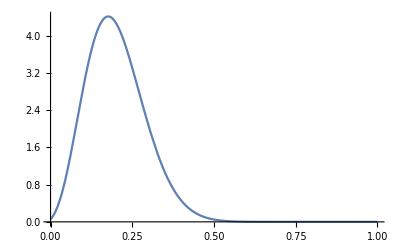

```mathematica
Plot[approx /. {x->0.2, t->0.05,Ne->500,α->0.005, Λ -> 1, W->1, VG->1}, {y,0,1}]
```